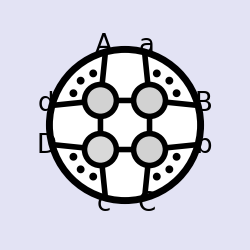
-Graphics-
One-Loop Amplitude Integrands
and Integrals in N=4 SYM
Jacob L. Bourjaily, 2013

```mathematica
<<loop_amplitudes.m
```

```mathematica
n=9;
(* fun *)
ab[___,j_,___,j_,___]:=0;
sortab={i_ab:>ordercup[i]Signature[i]/Signature[ordercup[i]]};
sortdoubleab={i_doubleab:>Sort[i]Signature[i]/Signature[Sort[i]]};
sortcapinR=R[a__]:>R@@(Replace[List[a],cap[x_,y_]:>cap[ordercup@x,ordercup[y]],{0,Infinity}]);
Qlog[1]:=0;
Dmatrix[0]=0;
doubleab[___,j_,___,j_,___]:=0;
Dmatrix[ab[x__]y_]:=ab[x]Dmatrix[y];
FuseDmatrices:=Expand[#]//.{Dmatrix[i_]Dmatrix[j_]:>Dmatrix@Join[i,j]}&;
abelim={ab[x___,n+1,y___]:>ab[x,n,y]-e ab[x,B,y]};
abtre= ab[aa___,B,bb___]:>ab[aa,n-1,bb]-τ ab[aa,1,bb](ab[n-1,n,2,3]/ab[n,1,2,3])-e ab[aa,2,bb](ab[n-2,n-1,n,1]/ab[n-2,n-1,2,1]);
capexpand = {ab[x___, cap[{a_, b_}, {c__}], y___] :> ab[b, c] ab[x, a, y] + ab[c, a] ab[x, b, y],
               ab[x___,cap1[{a_,b_},{c__},{d__}],y___]:>(-1)^Length[{y}](ab[x,y,a,c]ab[x,y,b,d]-ab[x,y,a,d]ab[x,y,b,c])};
shifexp={ab[x___,shift[y_,z_],w___]:>ab[x,y⟦1⟧,w]+z ab[x,y⟦2⟧,w]};
mom=RandomInteger[{-100,100},{20,4}];
mom1=Table[Binomial[n+i,i],{n,20},{i,0,3}];
neab[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[mom[[{x}]]];
neab1[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[mom1[[{x}]]];
todmatrix:=FuseDmatrices[#/.i_R:>(fromRform[n+1][i][[1,1]])Dmatrix[fromRform[n+1][i][[1,2]]]//.shifexp//.capexpand]&;
todmatrixn:=FuseDmatrices[#/.i_R:>(fromRform[n][i][[1,1]])Dmatrix[fromRform[n][i][[1,2]]]//.shifexp//.capexpand]&;
DmatrixEval[fermions__] :={Dmatrix[i_/;Length[i]==Length[{fermions}[[1]]]]:>Product[Det[Array[i[[#1,{fermions}[[l,#2]]]]&,{Length[i],Length[i]}]],{l,1,4}],Dmatrix[i_]:>0};
order[exprn_,option_:1]:=If[option==0,exprn/.{ab[x__]:>Signature[{x}] ab@@Sort[{x}]},Block[{nGuess=Max[Join[{0},Flatten[Apply[List,Cases[exprn,_ab,{0,∞}],{1}]]]],consec,xLike},consec=Partition[Range[nGuess],2,1,1];xLike=Apply[If[Length[Range[#2,#3]]>Length[Range[#4,#1+nGuess]],{#3,#4,#1,#2},{##1}]&,Select[Flatten/@Subsets[consec,{2}],Length[#1∩#1]==4&],{1}];exprn/.{ab[x__]:>If[Length[{x}]==2,(If[Length[#1]==1,Signature[#1[[1]]] Signature[{x}] ab@@#1[[1]],Signature[{x}] ab@@Sort[{x}]]&)[Select[consec,Length[{x}∩#1]==2&,1]],(If[Length[#1]==1,Signature[#1[[1]]] Signature[{x}] ab@@#1[[1]],Block[{xLikeLines=Select[consec,Length[#1∩{x}]==2&],boundaries},If[Length[xLikeLines]==0,Signature[{x}] ab@@Sort[{x}],boundaries=Complement[{x},xLikeLines[[1]]];If[Length[Range[boundaries[[2]],If[xLikeLines[[1,1]]<boundaries[[2]],nGuess,0]+xLikeLines[[1,1]]]]+Length[Range[xLikeLines[[1,2]],If[boundaries[[1]]<xLikeLines[[1,2]],nGuess,0]+boundaries[[1]]]]>Length[Range[boundaries[[1]],If[xLikeLines[[1,1]]<boundaries[[1]],nGuess,0]+xLikeLines[[1,1]]]]+Length[Range[xLikeLines[[1,2]],If[boundaries[[2]]<xLikeLines[[1,2]],nGuess,0]+boundaries[[2]]]],boundaries=Reverse[boundaries];];-Signature[Join[boundaries,xLikeLines[[1]]]] Signature[{x}] ab@@RotateLeft[Join[boundaries,xLikeLines[[1]]]]]]]&)[Select[xLike,Length[#1∩{x}]==4&]]]}]];
twistorSchouten=#1//.{ab[a___,x_,b___,y_,c___] ab[d___,x_,e___,y_,f___]:>Signature[Flatten[{x,y,Sort[{a,b,c}]}]] Signature[{a,x,b,y,c}] Signature[Flatten[{x,y,Sort[{d,e,f}]}]] Signature[{d,x,e,y,f}] ab@@Flatten[{x,y,Sort[{a,b,c}]}] ab@@Flatten[{x,y,Sort[{d,e,f}]}],ab[a___,x_,b___,y_,c___] ab[d___,y_,e___,x_,f___]:>Signature[Flatten[{x,y,Sort[{a,b,c}]}]] Signature[{a,x,b,y,c}] Signature[Flatten[{x,y,Sort[{d,e,f}]}]] Signature[{d,y,e,x,f}] ab@@Flatten[{x,y,Sort[{a,b,c}]}] ab@@Flatten[{x,y,Sort[{d,e,f}]}]}//.{ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,d_] ab[x_,y_,c_,b_]:>ab[x,y,a,c] ab[x,y,b,d],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,c_] ab[x_,y_,b_,d_]:>ab[x,y,a,d] ab[x,y,c,b],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]+ab[x_,y_,a_,d_] ab[x_,y_,b_,c_]:>ab[x,y,a,c] ab[x,y,b,d],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]+ab[x_,y_,a_,c_] ab[x_,y_,d_,b_]:>ab[x,y,a,d] ab[x,y,c,b],-ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,d_] ab[x_,y_,b_,c_]:>-ab[x,y,a,c] ab[x,y,b,d],-ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,c_] ab[x_,y_,d_,b_]:>-ab[x,y,a,d] ab[x,y,c,b]}&;
twistorSimplify[exprn_,orderQ_:0]:=If[Count[exprn,ab[x_,y_],∞]>0,Simplify[order[exprn]/.Apply[Rule,({#1,twistorSchouten[#1]}&)/@Cases[exprn,ab[x__] ab[y__]-ab[z__] ab[w__]|ab[x__] ab[y__]+ab[z__] ab[w__],{0,∞}],{1}]],order[FullSimplify[If[orderQ==1,order[FullSimplify[order[exprn,0],TransformationFunctions->{Automatic,twistorSchouten}],1],exprn],TransformationFunctions->{Automatic,twistorSchouten}],1]];
toqlog={R[i_,j_,k_,n,n+1]:> Which[i===1&&k===n-1,dlog[ab[X,n-2,n-1]/ab[X,1,2]]Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,j]],k===n-1,dlog[ab[X,i,j]/ab[X,n-2,n-1]]Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]],i===1,dlog[ab[X,j,k]/ab[X,1,2]]Qlog[ab[n-1,n,1,k]/ab[n-1,n,1,j]],True,dlog[ab[X,i,j]/ab[X,j,k]]Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]]+dlog[ab[X,j,k]/ab[X,i,k]]Qlog[ab[n-1,n,1,k]/ab[n-1,n,1,i]]]};
dab[___,i_,___,i_,___]:=0;
sortdab={i_dab:>(Sort[i] Signature[i])/Signature[Sort[i]]};
dabRcanel[exp_]:=Expand[exp]/.R[x__]dab[y__]:>0/;Sort[{x}]==Sort[{y}];
qlogRcanel[exp_]:=Expand[exp]/.R[x__]Qlog[ab[z__]/ab[y__]]:>0/;Sort[{x}]==Sort[Union[{y},{z}]];
qlogtodab=Qlog[ab[1,i_,n-1,n]/ab[1,j_,n-1,n]]:>dab[1,i,j,n-1,n]/(ab[1,i,n-1,n]ab[1,j,n-1,n]);
Rtodab=R[i_,j_,k_,n,n+1]:>(dab[i,j,k,n,B] ab[i,j,k,n])/(ab[i,j,n,B]ab[j,k,n,B]ab[k,i,n,B]);
dabBexp=dab[x___,B,y___]:>dab[x,n-1,y]-ab[n-1,n,2,3]/ab[n,1,2,3] τ dab[x,1,y]-ab[n-2,n-1,n,1]/ab[n-2,n-1,2,1] e dab[x,2,y];
dabtoqlog={dab[i_,j_,k_,l_,n]:>Which[i===1&&l===n-1,Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,k]]ab[1,j,n-1,n]ab[1,k,n-1,n],l===n-1, Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]]ab[n-1,n,1,i]ab[n-1,n,j,k]+Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,k]]ab[n-1,n,1,k]ab[n-1,n,i,j],
i===1,Qlog[ab[n-1,n,1,l]/ab[n-1,n,1,k]]ab[n-1,n,1,k]ab[n,1,l,j]+Qlog[ab[n-1,n,1,l]/ab[n-1,n,1,j]]ab[n-1,n,1,j]ab[n,1,k,l],True,dab[i,j,k,l,n]]};
dabcapexpand = {dab[x___, cap[{a_, b_}, {c__}], y___] :> ab[b, c] dab[x, a, y] + ab[c, a] dab[x, b, y]};
dabshifexp={dab[x___,shift[y_,z_],w___]:>dab[x,y⟦1⟧,w]+z dab[x,y⟦2⟧,w]};
fullabB[exp_]:=exp//.shifexp//.capexpand/.abelim/.abtre/.sortab

(* reduceR series *)
ab[___,j_,___,j_,___]:=0;

ordercup[exp_]:=SortBy[exp,Which[Head[#]===cap,1.5,Head[#]===shift,1.4,True,#]&];

sortR={i_R:>ordercup[i]Signature[i]/Signature[ordercup[i]]};
reduceR1[Rinv1_,Rinv2_]:=Switch[Rinv1,
_Plus,Total[(reduceR1[#1,Rinv2]&)/@List@@Rinv1],
_Times,((Rinv1 reduceR1[#1,Rinv2])/#1&)[FirstCase[Rinv1,_R]],
_R,With[{plist1=List@@Rinv1,plist2=List@@Rinv2},With[{foo=Sort[plist1∩plist2]},With[{i=Complement[plist1,foo],j=Complement[plist2,foo]},Which[!SubsetQ[foo,{n,n+1}],Rinv1,Length[foo]===4,(Signature[plist1]Signature[{foo[[1]],foo[[2]],i[[1]],foo[[3]],foo[[4]]}]  ab[foo[[1]],foo[[2]],foo[[3]],foo[[4]]]^3 ab[foo[[1]],foo[[3]],i[[1]],j[[1]]] ab[foo[[2]],foo[[3]],i[[1]],j[[1]]] ab[foo[[1]],foo[[2]],i[[1]],j[[1]]] R[foo[[1]],foo[[2]],foo[[3]],i[[1]],j[[1]]])/(ab[foo[[1]],foo[[2]],j[[1]],foo[[3]]]^3 ab[foo[[1]],i[[1]],foo[[3]],foo[[4]]] ab[foo[[2]],i[[1]],foo[[3]],foo[[4]]] ab[foo[[1]],foo[[2]],i[[1]],foo[[4]]]),Length[foo]===3,(Signature[plist1]  Signature[{foo[[1]],i[[1]],i[[2]],foo[[2]],foo[[3]]}](ab[j[[1]],j[[2]],foo[[2]],cap[i,foo]] ab@@Join[foo,{j[[2]]}] ab@@Join[foo,{j[[1]]}] ab@@Join[foo[[1;;2]],i] ab[cap[i,foo],foo[[1]],j[[1]],j[[2]]]) R[foo[[1]],j[[1]],j[[2]],foo[[2]],cap[i,foo]])/(ab[j[[1]],j[[2]],foo[[1]],foo[[2]]]^3 ab[i[[1]],i[[2]],foo[[2]],foo[[3]]] ab@@Join[foo,{i[[2]]}] ab@@Join[foo,{i[[1]]}] ab[foo[[3]],foo[[1]],i[[1]],i[[2]]]),Length[foo]===2,(Signature[plist1] Signature[Join[i,foo]](ab[j[[1]],i[[1]],n,n+1] ab[j[[1]],j[[2]],j[[3]],cap[foo,i]] ab@@Join[i,{n}] ab[j[[2]],j[[3]],n,n+1]) (R[cap[{i[[2]],i[[3]]},{n,n+1,i[[1]]}],i[[1]],cap[{j[[2]],j[[3]]},{n,n+1,j[[1]]}],j[[1]],n]/. cap[x_,y_]:>cap[Sort[x],Sort[y]]))/((ab@@Join[j,{n}])^2 ab[i[[3]],n,n+1,i[[1]]] ab[n,n+1,i[[1]],i[[2]]] ab@@Join[{n+1},i])]]]],
_,Rinv1]

prefreduceR[Rinv_]:=With[{ppp =MaximalBy[#,StringCount[ToString[#],"cap"]&]&@Select[List@@Rinv,(Head[#]===cap)&&IntersectingQ[First[List@@#],Complement[List@@Rinv,{#}]]&]},
If[Length@ppp==0,Rinv,With[{pp=First@ppp},
With[{qq= DeleteCases[List@@Rinv,pp]},
With[{bbbb1=First[Intersection[First@pp,qq]],bbbb2=First@Complement[First@pp,Intersection[First@pp,qq]]},
(1+(ab@@(Join[{bbbb1},DeleteCases[List@@Rinv,pp|bbbb1]]))(ab@@(Join[{bbbb2},Last@pp]))/((ab@@(Join[Last@pp,{bbbb1}]))(ab@@(Join[{bbbb2},DeleteCases[List@@Rinv,pp|bbbb1]]))))^(-1) Rinv/.pp->bbbb2]
]]]];

freduceR[$Rinv_]:=With[{Rinv=Expand[$Rinv]},Switch[Rinv,
	_Plus, Total[freduceR/@ (List @@ Rinv)],
	_Times, (Rinv/# freduceR[#]) &[FirstCase[Rinv, _R]],
	_R, If[!Rinv===prefreduceR[Rinv],freduceR[prefreduceR[Rinv]],
	With[{cc=Cases[Rinv,_cap,1],pp=Cases[Rinv,Except[_cap],1]},
If[
Length[cc]>=1,With[{plist=List@@Rinv,c=First[cc]},
With[{foo=Intersection[pp,First[c]]},With[{pl=First[Complement[First[c],foo]]},
If[!Length[foo]==1,((prefreduceR/@(R@@@RotateLeft[Partition[Join[plist,{pl}],5,1,1]])).{1,-1,1,-1,1,0}),Rinv]]]],
Rinv
]]]]];
redR[exp_]:=FixedPoint[#/.i_R:>prefreduceR[i]&,exp];

fuse:=Expand[#]/.{doubleab[i_] Dmatrix[j_]:>doubleab@Join[i,j] Dmatrix[j]}&;
DmatrixEval3[a_,k_]:=With[{fermions=Transpose[{a}]},{Dmatrix[i_/;Length[i]==Length[fermions[[1]]]]:>Product[Det[Array[i[[#1,fermions[[l,#2]]]]&,{Length[i],Length[i]}]],{l,k}],Dmatrix[i_]:>0}]
dabne[fermions__]:={doubleab[i_/;Length[i]==Length[{fermions}[[1]]]]:>Product[Det[Array[i[[#1,{fermions}[[l,#2]]]]&,{Length[i],Length[i]}]],{l,1}],doubleab[i_]:>0}

sortall=Join[sortR,sortab,sortdab,{sortcapinR}];
todoubleab:=FuseDmatrices[#1/.i_dab:> doubleab[fromRform[n][R@@i]⟦1,2⟧]//.shifexp//.capexpand]&
expandlog[exp_]:=Block[{a,b,x},exp/.{log[a_]:>Total[#[[2]]log[#[[1]]]&/@ FactorList[a]]}/.{log[a_^x_]:>x log[a]}];

sixR[a_,b_,c_,d_,e_,f_]:=R[a,b,c,d,f]+R[a,b,c,f,e]+R[a,b,d,e,f]+R[a,c,d,f,e]+R[b,c,d,e,f]
myComplement[x_,y_]:=Select[x,!MemberQ[y,#]&];
```

```mathematica
randomPositiveZs[n_]:=(Zs=Nest[Function[{mat},Block[{hatted=Append[(Append[Total[mat⟦#1;;-1⟧],1]&)/@Range[2,Length[mat]],Append[PadRight[{},Length[mat⟦1⟧]],1]],newRow=RandomInteger[{1,10},{Length[mat]}]},newRow hatted]],RandomInteger[{1,10},{n+8,1}],3];Zs=Transpose[Inverse[Transpose[Zs⟦{1,2,3,4}⟧]].Transpose[Zs]]⟦5;;-1⟧;)
neabp[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[Zs⟦{x}⟧];
```

```mathematica
dabtoeta=dab[x__]:>Apply[ab,Partition[{x},4,1,5],{1}].η/@{x};
abfactor[exp_]:=Module[{lis=Union@@Cases[exp//.shifexp//.capexpand,_ab,Infinity]/.ab->List},If[Position[exp/(ab@@@Subsets[lis,{4}])//neab,_Integer]=!={},ab@@@Subsets[lis,{4}][[Flatten[Position[exp/(ab@@@Subsets[lis,{4}])//neab,_Integer]]]],exp]];
ordercup2[exp_]:=SortBy[exp,If[Head[#]===cap,If[(#/.cap:>List)[[1]]=={8,9},10,0.5], #]&];

sortR2={i_R:>ordercup2[i]Signature[i]/Signature[ordercup2[i]]};
repR1={R[cap[{a_,b_},{c_,n,n+1}],x___,a_,y___,cap[{n,n+1},m__]]:>(ab[a,b,n,n+1]ab[c,x,a,y])/ab[x,a,y,cap[{n,n+1},{a,b,c}]] R[c,cap[{a,b},{c,n,n+1}],x,a,y]R[a,b,c,n,n+1],R[cap[{b_,a_},{c_,n,n+1}],x___,a_,y___,cap[{n,n+1},m__]]:>(ab[a,b,n,n+1]ab[c,x,a,y])/ab[x,a,y,cap[{n,n+1},{a,b,c}]] R[c,cap[{a,b},{c,n,n+1}],x,a,y]R[a,b,c,n,n+1]};
repR2={R[cap[{a___},{c_,n,n+1}],d___,n+1,cap[{n,n+1},m__]]:>(ab[c,d,n+1]ab[a,n,n+1])/(ab[c,a,n+1]ab[d,n,n+1])R[c,cap[{a},{c,n,n+1}],d,n]R[a,c,n,n+1]};
qlogtodabm={Qlog[ab[7,8,1,i_]/ab[7,8,1,j_]]:>dab[1,i,j,n-1,n]/(ab[1,i,n-1,n] ab[1,j,n-1,n])};
numabfactor[exp_]:=ab@@@Subsets[Range[9],{4}][[Flatten[Position[exp/(ab@@@Subsets[Range[9],{4}])//neab,_Integer]]]];
dabsimp[exp_]:=Module[{f1,f2,f3},f1=exp/.dabcapexpand/.dabtoeta//neab//Simplify;
f2=dab@@(Cases[f1,η[_],Infinity]/.η->List//Flatten);
f3=Times@@(exp/f2/.dabcapexpand/.dabtoeta//neab//Simplify//numabfactor);
If[Abs[( exp/(f2*f3)/.dabcapexpand/.dabtoeta//neab//Simplify)/.i_η:>1//neab]<10,f2*f3 ( exp/(f2*f3)/.dabcapexpand/.dabtoeta//neab//Simplify)/.sortall,exp]
];

absim[exp_]:=Module[{f1},f1=Times@@(exp//numabfactor);
If[Abs[exp/f1//neab]<10,f1(exp/f1//neab),exp]
];
```

```mathematica
utoab={u->(ab[1,2,3,9] ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7]),v->(ab[1,6,7,9] ab[2,3,4,5])/(ab[1,4,5,9] ab[2,3,6,7]),u1->(ab[2,3,4,5] ab[6,7,8,9])/(ab[2,3,6,7] ab[4,5,8,9]),v1->(ab[4,5,6,7] ab[8,9,2,3])/(ab[2,3,6,7] ab[4,5,8,9])};
tautre={τ->(-t^2-2 t(-1+u1) u+u^2 v1 (-2-2 u1+v1))/(t^2+2 t (-1+v) v1+(2+2 v-u) u v1^2)};
deltatau=(u^2+τ^2((1-u-v)^2-4u v)-2τ u v-2τ u+2τ u^2+2τ u/v1-2τ (u v)/v1-(2 u^2)/v1-2τ u^2/v1+u^2/v1^2+(u^2 u1^2)/v1^2-2τ (u u1)/v1-(2 u^2 u1)/v1^2-2(u^2 u1)/v1-2τ(u^2 u1)/v1+2τ (u v u1)/v1)/(τ+u/v1)^2
(* 1-u-v+Δ= (4 u v1 (u ((-2+u) u1-v (-2+v1)) v1+t (u u1-v v1)))/((t+u v1) (t (u-v1)+u v1 (-u-2 u1+2 v+v1))),1-u-v-Δ= -(2 (t-u v1) (t (u (-1+u1)+v1-v v1)+u v1 (u (1+u1)-(1+v) v1)))/((t+u v1) (t (u-v1)+u v1 (-u-2 u1+2 v+v1))), integration range= [v1(1-v+Δ),u(1-u1+Δ1)] *)
deltat=(t^2 (u (-1+u1)+v1-v v1)+u^2 v1^2 (u (-1+u1)-4 u1+4 v+v1-v v1)+2 t u v1 (u (1+u1)-(1+v) v1))/((t+u v1) (t (u-v1)+u v1 (-u-2 u1+2 v+v1)))
shiftp4=shift[{6,7},-(u(v1-(2 ab[2,3,8,9] ab[4,5,6,9])/(ab[2,3,6,9] ab[4,5,8,9]))+t)/(u(v1-(2 ab[2,3,8,9] ab[4,5,7,9])/(ab[2,3,7,9] ab[4,5,8,9]))+t) ab[2,3,6,9]/ab[2,3,7,9]];
shiftm4=shift[{6,7},-(-u v1(1+(2 ab[1,6,8,9] ab[2,3,4,5])/ab[cap[{2,3},{8,9,1}],4,5,6])+t)/(-u v1(1+(2 ab[1,7,8,9] ab[2,3,4,5])/ab[cap[{2,3},{8,9,1}],4,5,7])+t)ab[4,5,6,cap[{2,3},{8,9,1}]]/ab[4,5,7,cap[{2,3},{8,9,1}]]];
jacp4=(4 u v1 (u ((-2+u) u1-v (-2+v1)) v1+t (u u1-v v1)))/((t^2+2 t (-1+v) v1+u (2-u+2 v) v1^2)^2);
jacm4=-(2 (t-u v1) (t (u (-1+u1)+v1-v v1)+u v1 (u (1+u1)-(1+v) v1)))/((t^2+2 t (-1+v) v1+u (2-u+2 v) v1^2)^2);
```

```mathematica
-R[2,3,4,5,7]R[Subscript[δ, 2],cap[{2,3},{4,5,7}],3,9,10]+R[2,3,4,5,6]R[Subscript[δ, 2],cap[{2,3},{4,5,6}],3,9,10]+R[2,4,5,6,7]R[2,3,Subscript[δ, 2],9,10]-R[2,3,5,6,7]R[Subscript[δ, 2],cap[{2,3},{5,6,7}],3,9,10]+R[2,3,4,6,7]R[Subscript[δ, 2],cap[{2,3},{4,6,7}],3,9,10]-Numerator[Total[rForm[onShellGraph[2][{{3,4},{5,6},{7,8,9},{10,1,2}},{0,0,0,0}]]]]/.Subscript[δ, 2]:>shift[{6,7},(ab[6,10,9,cap[{2,3},{4,5,7}]]+ab[7,10,9,cap[{2,3},{4,5,6}]]+ab[6,7,2,3] √(-(4 ab[2,3,4,5] ab[4,5,6,7] ab[6,7,9,10] ab[9,10,2,3])/(ab[2,3,6,7]^2 ab[4,5,9,10]^2)+(1-(ab[2,3,4,5] ab[6,7,9,10])/(ab[2,3,6,7] ab[4,5,9,10])-(ab[4,5,6,7] ab[9,10,2,3])/(ab[2,3,6,7] ab[4,5,9,10]))^2) ab[9,10,4,5])/(2 ab[7,9,10,cap[{2,3},{4,5,7}]])];
```

```mathematica
(%1055//todmatrix)/.DmatrixEval[{2,3},{2,9},{2,9},{2,9}]//neabp//Simplify
```

0

```mathematica
jacp4 Limit[(R[2,3,Subscript[δ, 2],9,10]/.Rtodab/.dabBexp/.Subscript[δ, 2]:>shiftp4//fullabB)/.tautre/.utoab/.dabshifexp//Simplify,e->0]/.utoab//neab//Simplify//Factor
```

(37618451332530730454624809168138653486246545318394383562708704 (326073255260852029803827048539015917033835049975955983744954934708077842693586112453552066975963 dab[2,3,6,9,1]-113207473970023878155780245260159436402501936320664790591651141297791596914367852238776157840704 t dab[2,3,6,9,1]-11242975043001145772124717085263881398682172952422017067525254130247017715179460668159579783168 t^2 dab[2,3,6,9,1]+2721471065923197831318679479944387006573229039416538768870960895779209059463444760404023050240 t^3 dab[2,3,6,9,1]+68504627636501279488062942850521810853161086339358627303447188963346420597731589122630142352659 dab[2,3,6,9,8]-30994090360581901116242477090679706048888183260921588195536770477195470574305118337851858383168 t dab[2,3,6,9,8]+1389952919669622634822146295936460694733299323269450625162113219921953005281770030910653333504 t^2 dab[2,3,6,9,8]+187400404985364823068676466721690471768369287020772382517618653527765662205698677403712225280 t^3 dab[2,3,6,9,8]-911644664128851327329675712692578122860439791329485096311462061173191457711258942608386121931179 dab[2,3,7,9,1]-94716106525865303991550803011071470129970391877310605486794560011794568955711183157296703090880 t dab[2,3,7,9,1]+17885228450737334918460137981042049607501321368029826283776625051477376582480278595639996743680 t^2 dab[2,3,7,9,1]+1420148021277440137535635498036069136046828902027686766213675856862789592663915173537190510592 t^3 dab[2,3,7,9,1]-191527140743235724279985201550438758647912342361504958748992302695187554528011548545904838286947 dab[2,3,7,9,8]+260069436567456630533398809670288409208474015677434370019430988284373247656516756852675742528 t dab[2,3,7,9,8]+2360893587518420637180885324913464253342000047036519092582343473630960091467040574738617630720 t^2 dab[2,3,7,9,8]+97791344416250857508399999278498366092546316781199611851485033810259205799561566029190529024 t^3 dab[2,3,7,9,8]))/(18506123 (-116847932340016898498603881945123693491+18219707105273727404327332454454133888 t) (-7141391825286191864565102036178328617525+1288280999097825440008308968744102322432 t) (-79762712801530300374913300908727622002811+3657405541977327685712304878264143661184 t) (-172995216974872248190224957476648861664132116339+21386840631981057926394537382808547442676699520 t))

```mathematica
-7141391825286191864565102036178328617525//numabfactor
```

{}

```mathematica
(ab[2,3,8,9]/ab[1,2,3,9] Residue[%1131,{t,116847932340016898498603881945123693491/18219707105273727404327332454454133888}])/(dab[1,2,cap[{6,7},{2,4,5}],8,9]/(ab[1,2,8,9]ab[1,cap[{6,7},{2,4,5}],8,9])/.dabcapexpand/.dabtoeta//neab//Simplify)/.dabtoeta//neab//Simplify
```

```mathematica
dab[1,2,cap[{6,7},{2,4,5}],8,9]/(ab[1,2,8,9]ab[1,cap[{6,7},{2,4,5}],8,9])/.dabtoqlog
```

Qlog[ab[8,9,1,2]/ab[8,9,1,cap[{6,7},{2,4,5}]]]

```mathematica
%1131
```

(37618451332530730454624809168138653486246545318394383562708704 (326073255260852029803827048539015917033835049975955983744954934708077842693586112453552066975963 dab[2,3,6,9,1]-113207473970023878155780245260159436402501936320664790591651141297791596914367852238776157840704 t dab[2,3,6,9,1]-11242975043001145772124717085263881398682172952422017067525254130247017715179460668159579783168 t^2 dab[2,3,6,9,1]+2721471065923197831318679479944387006573229039416538768870960895779209059463444760404023050240 t^3 dab[2,3,6,9,1]+68504627636501279488062942850521810853161086339358627303447188963346420597731589122630142352659 dab[2,3,6,9,8]-30994090360581901116242477090679706048888183260921588195536770477195470574305118337851858383168 t dab[2,3,6,9,8]+1389952919669622634822146295936460694733299323269450625162113219921953005281770030910653333504 t^2 dab[2,3,6,9,8]+187400404985364823068676466721690471768369287020772382517618653527765662205698677403712225280 t^3 dab[2,3,6,9,8]-911644664128851327329675712692578122860439791329485096311462061173191457711258942608386121931179 dab[2,3,7,9,1]-94716106525865303991550803011071470129970391877310605486794560011794568955711183157296703090880 t dab[2,3,7,9,1]+17885228450737334918460137981042049607501321368029826283776625051477376582480278595639996743680 t^2 dab[2,3,7,9,1]+1420148021277440137535635498036069136046828902027686766213675856862789592663915173537190510592 t^3 dab[2,3,7,9,1]-191527140743235724279985201550438758647912342361504958748992302695187554528011548545904838286947 dab[2,3,7,9,8]+260069436567456630533398809670288409208474015677434370019430988284373247656516756852675742528 t dab[2,3,7,9,8]+2360893587518420637180885324913464253342000047036519092582343473630960091467040574738617630720 t^2 dab[2,3,7,9,8]+97791344416250857508399999278498366092546316781199611851485033810259205799561566029190529024 t^3 dab[2,3,7,9,8]))/(18506123 (-116847932340016898498603881945123693491+18219707105273727404327332454454133888 t) (-7141391825286191864565102036178328617525+1288280999097825440008308968744102322432 t) (-79762712801530300374913300908727622002811+3657405541977327685712304878264143661184 t) (-172995216974872248190224957476648861664132116339+21386840631981057926394537382808547442676699520 t))

```mathematica
38520768366950525608323605987632//numabfactor
```

{ab[1,4,5,9]}

```mathematica
(sixR[2,3,Subscript[δ, 2],9,10,7]/.Subscript[δ, 2]:>shiftp4/.sortR//.Rtodab/.R[__]:>0)/.dabshifexp/.shifexp
```

(ab[2,3,7,9] dab[2,3,7,9,B])/(ab[2,3,9,B] ab[3,7,9,B] ab[7,2,9,B])+(ab[6,2,7,9] dab[6,2,7,9,B])/(ab[2,7,9,B] (ab[6,2,9,B]-(ab[2,3,6,9] (t+u (v1-(2 ab[2,3,8,9] ab[4,5,6,9])/(ab[2,3,6,9] ab[4,5,8,9]))) ab[7,2,9,B])/(ab[2,3,7,9] (t+u (v1-(2 ab[2,3,8,9] ab[4,5,7,9])/(ab[2,3,7,9] ab[4,5,8,9]))))) ab[7,6,9,B])-(ab[6,3,7,9] dab[6,3,7,9,B])/(ab[3,7,9,B] (ab[6,3,9,B]-(ab[2,3,6,9] (t+u (v1-(2 ab[2,3,8,9] ab[4,5,6,9])/(ab[2,3,6,9] ab[4,5,8,9]))) ab[7,3,9,B])/(ab[2,3,7,9] (t+u (v1-(2 ab[2,3,8,9] ab[4,5,7,9])/(ab[2,3,7,9] ab[4,5,8,9]))))) ab[7,6,9,B])

```mathematica
(Limit[(ab[2,3,7,9] dab[2,3,7,9,B])/(ab[2,3,9,B] ab[3,7,9,B] ab[7,2,9,B])/.dabBexp//fullabB,e->0]//Simplify)//Simplify//Factor
```

(ab[1,2,3,9] ab[2,3,7,9] (τ ab[2,3,8,9] dab[2,3,7,9,1]+ab[1,2,3,9] dab[2,3,7,9,8]))/((1+τ) ab[2,3,8,9] (τ ab[1,2,7,9] ab[2,3,8,9]+ab[1,2,3,9] ab[2,7,8,9]) (τ ab[1,3,7,9] ab[2,3,8,9]+ab[1,2,3,9] ab[3,7,8,9]))

```mathematica
jacp4/(1+τ)/.tautre//Simplify
```

(2 u v1 (u ((-2+u) u1-v (-2+v1)) v1+t (u u1-v v1)))/((t^2+2 t (-1+v) v1+u (2-u+2 v) v1^2) (t (u-u u1+(-1+v) v1)+u v1 (-u (1+u1)+(1+v) v1)))

```mathematica
(t ab[1,4,5,9] ab[2,3,6,7]^2 ab[4,5,8,9] (ab[1,2,3,9] (ab[2,3,6,7] ab[4,5,8,9]-ab[2,3,4,5] ab[6,7,8,9])+(ab[1,6,7,9] ab[2,3,4,5]-ab[1,4,5,9] ab[2,3,6,7]) ab[8,9,2,3])+ab[1,2,3,9] ab[4,5,6,7]^2 ab[8,9,2,3] (-ab[1,2,3,9] (ab[2,3,6,7] ab[4,5,8,9]+ab[2,3,4,5] ab[6,7,8,9])+(ab[1,6,7,9] ab[2,3,4,5]+ab[1,4,5,9] ab[2,3,6,7]) ab[8,9,2,3]))
```

```mathematica
Simplify[(1/(ab[1,4,5,9] ab[2,3,6,7]^2 ab[4,5,8,9] (ab[1,2,3,9] (ab[2,3,6,7] ab[4,5,8,9]-ab[2,3,4,5] ab[6,7,8,9])+(ab[1,6,7,9] ab[2,3,4,5]-ab[1,4,5,9] ab[2,3,6,7]) ab[8,9,2,3])))ab[1,2,3,9] ab[4,5,6,7]^2 ab[8,9,2,3] (-ab[1,2,3,9] (ab[2,3,6,7] ab[4,5,8,9]+ab[2,3,4,5] ab[6,7,8,9])+(ab[1,6,7,9] ab[2,3,4,5]+ab[1,4,5,9] ab[2,3,6,7]) ab[8,9,2,3])/.sortab]
```

```mathematica
(ab[1,2,3,9] ab[2,3,8,9] ab[4,5,6,7]^2 ((ab[1,6,7,9] ab[2,3,4,5]+ab[1,4,5,9] ab[2,3,6,7]) ab[2,3,8,9]-ab[1,2,3,9] (ab[2,3,6,7] ab[4,5,8,9]+ab[2,3,4,5] ab[6,7,8,9])))/(ab[1,4,5,9] ab[2,3,6,7]^2 ab[4,5,8,9] ((ab[1,6,7,9] ab[2,3,4,5]-ab[1,4,5,9] ab[2,3,6,7]) ab[2,3,8,9]+ab[1,2,3,9] (ab[2,3,6,7] ab[4,5,8,9]-ab[2,3,4,5] ab[6,7,8,9])))//neab
```

```mathematica
((ab[1,2,3,9] ab[2,3,8,9] ab[4,5,6,7]^2)/(ab[1,4,5,9] ab[2,3,6,7]^2 ab[4,5,8,9]))/□/.utoab/.sortab
```

1

```mathematica
-172995216974872248190224957476648861664132116339/21386840631981057926394537382808547442676699520/u v1-1/.utoab//neab
```

-7607854168823203564290865859894049404894179439401/71027166069585232095783591474070305822399109440

```mathematica
7607854168823203564290865859894049404894179439401//numabfactor
```

{}

```mathematica
u v1((v+1) ab[2,3,8,9]-ab[1,2,3,9] (1+u1))/((v-1) ab[2,3,8,9]+ab[1,2,3,9] (1-u1))/.utoab//neab//Simplify
```

-47994964036868589070472999689857678936382228011130550953/3168994461790595373282109125214714988413283385718880640

```mathematica
utoab
```

{u→(ab[1,2,3,9] ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7]),v→(ab[1,6,7,9] ab[2,3,4,5])/(ab[1,4,5,9] ab[2,3,6,7]),u1→(ab[2,3,4,5] ab[6,7,8,9])/(ab[2,3,6,7] ab[4,5,8,9]),v1→(ab[4,5,6,7] ab[8,9,2,3])/(ab[2,3,6,7] ab[4,5,8,9])}

```mathematica
(-1594323919640422639321113208104795909096641584180224+197101123264337429849652056519963573231708462776320 t)/(-172995216974872248190224957476648861664132116339+21386840631981057926394537382808547442676699520 t)//Simplify
```

9216

```mathematica
6922734633491784119/ab[1,2,8,9]//neab
```

-1359670664161

```mathematica
ab[1,8,9,cap[{2,4},{5,6,7}]]//neab
```

-46546088725729

```mathematica
1274331 *2//numabfactor
```

{ab[1,2,3,9]}

```mathematica
256225957247517752791321274//numabfactor
```

{ab[1,2,8,9],ab[2,3,8,9]}

```mathematica
-184424528158365716//numabfactor
```

```mathematica
(18219707105273727404327332454454133888 *9)/(ab[1,4,5,9]ab[2,3,6,7]ab[4,5,8,9])//neab
```

-23474263763760746

```mathematica
-434417612546599308047758//numabfactor
```

{ab[2,3,8,9]}

```mathematica
18506123*3//numabfactor
```

{}

```mathematica
Collect[Denominator[%1119],t]//neab
```

-1175080106902362477118571945529386199762573146458716010760321237655334040885103106070231431247318183298620200838073375129354428579688894901332860208755977334116545682779093220011242215280454240238391377317398593364313985212901591083302601139476661409151741109374812160000+806339614021877742482106782699554807380322709707823795843107470173738589088312439141451948446710273693509671574793027727984429293445948636778816444850099851022554226453494158511110689349699533857922556518465378658373256672173265976182900035578925782277872824750807449600 t-213914573115012738219022428862226058493451330112750726042934956550190109201847240937228696057792093464065381606058389162105461949550211547004951464186229386488721813140178979055385120493270419311845022468261159749649279485169310561913772234285103617290962202787152134144 t^2+27089474780079312817481164954871832312319995690617023555490640223524469701887152127635349773312410251215470074257421409398563189430728695904102592054345841007430988852028219708322148425194816139361593544557604093325100185250680911699138098186839829489641011738310606848 t^3-1602077132479769837795793158573424272989694123761051453744172742815449183624739843817204451014947411616386039295526225015654026674611753798396714214675874870160670762937528582431679022479431654864067958709794645311925517455096269721676514327765452565020808186836287488 t^4+33800961301588109409891617311993603918298045362732419455008489541136529972758751281547204858847041626618577725569761531148797185303504835275177352164547482352930083775373750555722251373944955669999534524097232190928149243940151593200317245746043285052141658062192640 t^5

```mathematica
(-ab[1,2,7,9] ab[2,3,6,9] ab[2,3,8,9]+ab[1,2,6,9] ab[2,3,7,9] ab[2,3,8,9]-ab[1,2,3,9] ab[2,3,7,9] ab[2,6,8,9]+ab[1,2,3,9] ab[2,3,6,9] ab[2,7,8,9]) /18219707105273727404327332454454133888//neab
```

0

```mathematica
2813944550347514687989059//numabfactor
```

{}

```mathematica
346686915302554730474912453888688/(ab[1,4,5,9]ab[4,5,8,9]ab[2,3,6,7])//neab
```

-198520573751/4

```mathematica
6619258388221725434/ab[1,4,5,9]//neab
```

198520573751

```mathematica
(ab@@@Subsets[Range[9],{4}])/198520573751//neab
```

{3162862/198520573751,-55484632/198520573751,-6565626/198520573751,10368726/198520573751,-29095954/198520573751,-2548662/198520573751,58453272/198520573751,4987482/198520573751,-9210035/198520573751,31483716/198520573751,3311285/198520573751,33847104/198520573751,-30058396/198520573751,-14578152/198520573751,-10986188/198520573751,2768319/198520573751,-19474374/198520573751,-2854773/198520573751,18486823/198520573751,3433770/198520573751,-5091479/198520573751,-42045164/198520573751,-756666/198520573751,9479475/198520573751,-20840314/198520573751,-577631/198520573751,-74005596/198520573751,-28458528/198520573751,-21191884/198520573751,-23747248/198520573751,-17197407/198520573751,36300600/198520573751,589347/198520573751,18883803/198520573751,5745012/198520573751,-11479537/198520573751,52316508/198520573751,52758830/198520573751,33372768/198520573751,33342934/198520573751,12744720/198520573751,-25330866/198520573751,-118686/198520573751,-33674905/198520573751,-8242295/198520573751,16068437/198520573751,57452454/198520573751,32372004/198520573751,29139870/198520573751,-4003294/198520573751,-7229992/198520573751,-2043322/198520573751,35703693/198520573751,7229043/198520573751,-14035647/198520573751,3989341/198520573751,10013166/198520573751,-1189850/198520573751,-855146/198520573751,4713060/198520573751,-3610558/198520573751,41658818/198520573751,-17824462/198520573751,9434562/198520573751,71407054/198520573751,5675808/198520573751,-20729330/198520573751,6536184/198520573751,7583998/198520573751,-12525480/198520573751,37012246/198520573751,-37779426/198520573751,13353579/198520573751,-12570228/198520573751,-77210253/198520573751,-4813231/198520573751,19275960/198520573751,-4447763/198520573751,-5211822/198520573751,11408970/198520573751,-40874394/198520573751,-11694965/198520573751,-16700862/198520573751,-51808825/198520573751,9794343/198520573751,42213570/198520573751,16893561/198520573751,-8094797/198520573751,-5223780/198520573751,28400281/198520573751,-24843750/198520573751,18212638/198520573751,-18642863/198520573751,3324882/198520573751,49825259/198520573751,3770703/198520573751,-8967530/198520573751,646469/198520573751,8490988/198520573751,-10977448/198520573751,24650956/198520573751,-45141483/198520573751,-3327380/198520573751,77413135/198520573751,11646967/198520573751,44254084/198520573751,23235355/198520573751,-22915635/198520573751,17629764/198520573751,-37998535/198520573751,-27013816/198520573751,46050646/198520573751,10318902/198520573751,-47554120/198520573751,-18969621/198520573751,-77305683/198520573751,-36911391/198520573751,24810797/198520573751,-11480093/198520573751,23048399/198520573751,46379124/198520573751,-17162947/198520573751,-77872375/198520573751,-35172715/198520573751,3266319/198520573751,-46234051/198520573751}

```mathematica
-(2 (t-u v1) (t (u (-1+u1)+v1-v v1)+u v1 (u (1+u1)-(1+v) v1)))/(t^2 (u (-1+u1)+v1-v v1)+u^2 v1^2 (u (-1+u1)-4 u1+4 v+v1-v v1)+2 t u v1 (u (1+u1)-(1+v) v1))D[(-t^2-2 t(-1+u1) u+u^2 v1 (-2-2 u1+v1))/(t^2+2 t (-1+v) v1+(2+2 v-u) u v1^2),t]//Simplify
```

```mathematica
(((Limit[-(4 ab[2,3,4,5] ab[4,5,6,7] ab[6,7,9,10] ab[9,10,2,3])/(ab[2,3,6,7]^2 ab[4,5,9,10]^2)+(1-(ab[2,3,4,5] ab[6,7,9,10])/(ab[2,3,6,7] ab[4,5,9,10])-(ab[4,5,6,7] ab[9,10,2,3])/(ab[2,3,6,7] ab[4,5,9,10]))^2//fullabB,e->0]/.sortab//Simplify//Simplify))//Simplify)-deltatau/.utoab//neab//Simplify
```

0

```mathematica
Limit[(1-(ab[2,3,4,5] ab[6,7,9,10])/(ab[2,3,6,7] ab[4,5,9,10])-(ab[4,5,6,7] ab[9,10,2,3])/(ab[2,3,6,7] ab[4,5,9,10]))//fullabB,e->0]+deltat-(4 u v1 (u ((-2+u) u1-v (-2+v1)) v1+t (u u1-v v1)))/((t+u v1) (t (u-v1)+u v1 (-u-2 u1+2 v+v1)))/.tautre/.utoab//neabp//Simplify
```

0

```mathematica
Limit[(1-(ab[2,3,4,5] ab[6,7,9,10])/(ab[2,3,6,7] ab[4,5,9,10])-(ab[4,5,6,7] ab[9,10,2,3])/(ab[2,3,6,7] ab[4,5,9,10]))//fullabB,e->0]-deltat-( -(2 (t-u v1) (t (u (-1+u1)+v1-v v1)+u v1 (u (1+u1)-(1+v) v1)))/((t+u v1) (t (u-v1)+u v1 (-u-2 u1+2 v+v1))))/.tautre/.utoab//neabp//Simplify
```

0

```mathematica
(-4 (1+τ) ab[1,2,3,9] ab[2,3,4,5] ab[2,3,8,9] ab[4,5,6,7] (τ ab[1,6,7,9] ab[2,3,8,9]+ab[1,2,3,9] ab[6,7,8,9])+((1+τ) ab[1,2,3,9] ab[2,3,8,9] ab[4,5,6,7]-ab[2,3,6,7] (τ ab[1,4,5,9] ab[2,3,8,9]+ab[1,2,3,9] ab[4,5,8,9])+ab[2,3,4,5] (τ ab[1,6,7,9] ab[2,3,8,9]+ab[1,2,3,9] ab[6,7,8,9]))^2)/(ab[2,3,6,7]^2 ( ab[1,4,5,9] ab[2,3,8,9])^2)/.τ->-(ab[1,2,3,9] ab[6,7,8,9])/(ab[1,6,7,9] ab[2,3,8,9])//Simplify
```

```mathematica
Solve[((ab[1,2,3,9] (ab[1,6,7,9] (-ab[2,3,8,9] ab[4,5,6,7]+ab[2,3,6,7] ab[4,5,8,9])+(-ab[1,4,5,9] ab[2,3,6,7]+ab[1,2,3,9] ab[4,5,6,7]) ab[6,7,8,9]))/(ab[1,4,5,9] ab[1,6,7,9] ab[2,3,6,7] ab[2,3,8,9])+(τ+(ab[1,2,3,9] ab[6,7,8,9])/(ab[1,6,7,9] ab[2,3,8,9]))t)^2==(-4 (1+τ) ab[1,2,3,9] ab[2,3,4,5] ab[2,3,8,9] ab[4,5,6,7] (τ ab[1,6,7,9] ab[2,3,8,9]+ab[1,2,3,9] ab[6,7,8,9])+((1+τ) ab[1,2,3,9] ab[2,3,8,9] ab[4,5,6,7]-ab[2,3,6,7] (τ ab[1,4,5,9] ab[2,3,8,9]+ab[1,2,3,9] ab[4,5,8,9])+ab[2,3,4,5] (τ ab[1,6,7,9] ab[2,3,8,9]+ab[1,2,3,9] ab[6,7,8,9]))^2)/(ab[2,3,6,7]^2 ( ab[1,4,5,9] ab[2,3,8,9])^2),τ]//Simplify
```

{{τ→-(ab[1,2,3,9] ab[6,7,8,9])/(ab[1,6,7,9] ab[2,3,8,9])},{τ→(ab[1,2,3,9] (2 ab[1,6,7,9] ((-1+t) ab[1,4,5,9] ab[2,3,6,7]+ab[1,2,3,9] ab[4,5,6,7]) (-ab[2,3,8,9] ab[4,5,6,7]+ab[2,3,6,7] ab[4,5,8,9])+((-1+t) ab[1,4,5,9] ab[2,3,6,7]+ab[1,2,3,9] ab[4,5,6,7])^2 ab[6,7,8,9]+ab[1,6,7,9]^2 ab[2,3,4,5] (2 ab[2,3,8,9] ab[4,5,6,7]+2 ab[2,3,6,7] ab[4,5,8,9]-ab[2,3,4,5] ab[6,7,8,9])))/(ab[1,6,7,9] ab[2,3,8,9] (ab[1,6,7,9]^2 ab[2,3,4,5]^2-(-1+t^2) ab[1,4,5,9]^2 ab[2,3,6,7]^2-2 ab[1,2,3,9] ab[1,4,5,9] ab[2,3,6,7] ab[4,5,6,7]+ab[1,2,3,9]^2 ab[4,5,6,7]^2-2 ab[1,6,7,9] ab[2,3,4,5] (ab[1,4,5,9] ab[2,3,6,7]+ab[1,2,3,9] ab[4,5,6,7])))}}

```mathematica
Collect[Denominator[τ/.%339[[2]]],t]/(ab[1,4,5,9]^2 ab[1,6,7,9] ab[2,3,6,7]^2 ab[2,3,8,9])//Expand
```

1-t^2+(ab[1,6,7,9]^2 ab[2,3,4,5]^2)/(ab[1,4,5,9]^2 ab[2,3,6,7]^2)-(2 ab[1,6,7,9] ab[2,3,4,5])/(ab[1,4,5,9] ab[2,3,6,7])-(2 ab[1,2,3,9] ab[1,6,7,9] ab[2,3,4,5] ab[4,5,6,7])/(ab[1,4,5,9]^2 ab[2,3,6,7]^2)-(2 ab[1,2,3,9] ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7])+(ab[1,2,3,9]^2 ab[4,5,6,7]^2)/(ab[1,4,5,9]^2 ab[2,3,6,7]^2)

```mathematica
(((ab[1,6,7,9]ab[2,3,8,9])/(ab[1,2,3,9]ab[6,7,8,9])Collect[Numerator[τ/.%339[[2]]],t])/(ab[1,4,5,9]^2 ab[1,6,7,9] ab[2,3,6,7]^2 ab[2,3,8,9])//Expand)-(1-2t+t^2-u^2+v^2-2v)/.{u->(ab[1,6,7,9] ab[2,3,4,5])/(ab[1,4,5,9] ab[2,3,6,7]),v->(ab[1,2,3,9] ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7]),u1->(ab[2,3,4,5] ab[6,7,8,9])/(ab[2,3,6,7] ab[4,5,8,9]),v1->(ab[4,5,6,7] ab[8,9,2,3])/(ab[2,3,6,7] ab[4,5,8,9])}/.sortab//Expand
```

(2 t ab[1,2,3,9] ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7])+(2 ab[1,6,7,9]^2 ab[2,3,4,5] ab[2,3,8,9] ab[4,5,6,7])/(ab[1,4,5,9]^2 ab[2,3,6,7]^2 ab[6,7,8,9])+(2 ab[1,6,7,9] ab[2,3,8,9] ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7] ab[6,7,8,9])-(2 t ab[1,6,7,9] ab[2,3,8,9] ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7] ab[6,7,8,9])-(2 ab[1,2,3,9] ab[1,6,7,9] ab[2,3,8,9] ab[4,5,6,7]^2)/(ab[1,4,5,9]^2 ab[2,3,6,7]^2 ab[6,7,8,9])-(2 ab[1,6,7,9] ab[4,5,8,9])/(ab[1,4,5,9] ab[6,7,8,9])+(2 t ab[1,6,7,9] ab[4,5,8,9])/(ab[1,4,5,9] ab[6,7,8,9])+(2 ab[1,6,7,9]^2 ab[2,3,4,5] ab[4,5,8,9])/(ab[1,4,5,9]^2 ab[2,3,6,7] ab[6,7,8,9])+(2 ab[1,2,3,9] ab[1,6,7,9] ab[4,5,6,7] ab[4,5,8,9])/(ab[1,4,5,9]^2 ab[2,3,6,7] ab[6,7,8,9])

```mathematica
+u^2-2u+2t u-v^2-(2v)/v1+(2v)/v1 t+(2u v)/v1+2 v^2/v1-(2 u v u1)/v1+2(v u1)/v1-2t(v u1)/v1+2(v v u1)/v1
```

```mathematica
Solve[((1-(ab[1,6,7,9] ab[2,3,4,5])/(ab[1,4,5,9] ab[2,3,6,7])-(ab[1,2,3,9] ab[4,5,8,9])/(ab[1,4,5,9] ab[2,3,8,9])+(ab[1,2,3,9] ab[2,3,4,5] ab[6,7,8,9])/(ab[1,4,5,9] ab[2,3,6,7] ab[2,3,8,9]))+(τ+1)t)^2==((-4 (1+τ) ab[1,2,3,9] ab[2,3,4,5] ab[2,3,8,9] ab[4,5,6,7] (τ ab[1,6,7,9] ab[2,3,8,9]+ab[1,2,3,9] ab[6,7,8,9])+((1+τ) ab[1,2,3,9] ab[2,3,8,9] ab[4,5,6,7]-ab[2,3,6,7] (τ ab[1,4,5,9] ab[2,3,8,9]+ab[1,2,3,9] ab[4,5,8,9])+ab[2,3,4,5] (τ ab[1,6,7,9] ab[2,3,8,9]+ab[1,2,3,9] ab[6,7,8,9]))^2)/(ab[2,3,6,7]^2 (ab[1,4,5,9] ab[2,3,8,9])^2)),τ]//neabp//Simplify
```

{{τ→-1},{τ→(1610981162663394+6207916487223724 t+5102143295825680 t^2)/(3544948999278505-5102143295825680 t^2)}}

```mathematica
Solve[τ==(1610981162663394+6207916487223724 t+5102143295825680 t^2)/(3544948999278505-5102143295825680 t^2),t]
```

{{t→(-2889020869-√(1225904842545313681+8548137837838790620 τ+15668674576810992100 τ^2))/(4748839160 (1+τ))},{t→(-2889020869+√(1225904842545313681+8548137837838790620 τ+15668674576810992100 τ^2))/(4748839160 (1+τ))}}

```mathematica
Solve[((1-(ab[1,6,7,9] ab[2,3,4,5])/(ab[1,4,5,9] ab[2,3,6,7])-(ab[1,2,3,9] ab[4,5,8,9])/(ab[1,4,5,9] ab[2,3,8,9])+(ab[1,2,3,9] ab[2,3,4,5] ab[6,7,8,9])/(ab[1,4,5,9] ab[2,3,6,7] ab[2,3,8,9]))-(τ+1)t)^2==((-4 (1+τ) ab[1,2,3,9] ab[2,3,4,5] ab[2,3,8,9] ab[4,5,6,7] (τ ab[1,6,7,9] ab[2,3,8,9]+ab[1,2,3,9] ab[6,7,8,9])+((1+τ) ab[1,2,3,9] ab[2,3,8,9] ab[4,5,6,7]-ab[2,3,6,7] (τ ab[1,4,5,9] ab[2,3,8,9]+ab[1,2,3,9] ab[4,5,8,9])+ab[2,3,4,5] (τ ab[1,6,7,9] ab[2,3,8,9]+ab[1,2,3,9] ab[6,7,8,9]))^2)/(ab[2,3,6,7]^2 (ab[1,4,5,9] ab[2,3,8,9])^2)),τ]//neabp//Simplify
```

{{τ→-1},{τ→(1610981162663394-6207916487223724 t+5102143295825680 t^2)/(3544948999278505-5102143295825680 t^2)}}

```mathematica
Solve[τ==(1610981162663394-6207916487223724 t+5102143295825680 t^2)/(3544948999278505-5102143295825680 t^2),t]
```

{{t→(2889020869-√(1225904842545313681+8548137837838790620 τ+15668674576810992100 τ^2))/(4748839160 (1+τ))},{t→(2889020869+√(1225904842545313681+8548137837838790620 τ+15668674576810992100 τ^2))/(4748839160 (1+τ))}}

```mathematica
Collect[Denominator[τ/.%140[[2]]],t]/(ab[1,4,5,9]^2 ab[2,3,6,7]^2 ab[2,3,8,9])//Expand
```

1-t^2+(ab[1,6,7,9]^2 ab[2,3,4,5]^2)/(ab[1,4,5,9]^2 ab[2,3,6,7]^2)-(2 ab[1,6,7,9] ab[2,3,4,5])/(ab[1,4,5,9] ab[2,3,6,7])-(2 ab[1,2,3,9] ab[1,6,7,9] ab[2,3,4,5] ab[4,5,6,7])/(ab[1,4,5,9]^2 ab[2,3,6,7]^2)-(2 ab[1,2,3,9] ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7])+(ab[1,2,3,9]^2 ab[4,5,6,7]^2)/(ab[1,4,5,9]^2 ab[2,3,6,7]^2)

```mathematica
((1-u-v)^2-4u v-t^2)/(%148)/.{u->(ab[1,6,7,9] ab[2,3,4,5])/(ab[1,4,5,9] ab[2,3,6,7]),v->(ab[1,2,3,9] ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7])}//Simplify
```

1

```mathematica
(τ/.%140[[2]])-(1-2t+t^2+u^2-2u+2t u-v^2-(2v)/v1+(2v)/v1 t+(2u v)/v1+2 v^2/v1-(2 u v u1)/v1+2(v u1)/v1-2t(v u1)/v1+2(v v u1)/v1)/((1-u-v)^2-4u v-t^2)/.{u->(ab[1,6,7,9] ab[2,3,4,5])/(ab[1,4,5,9] ab[2,3,6,7]),v->(ab[1,2,3,9] ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7]),u1->(ab[2,3,4,5] ab[6,7,8,9])/(ab[2,3,6,7] ab[4,5,8,9]),v1->(ab[4,5,6,7] ab[8,9,2,3])/(ab[2,3,6,7] ab[4,5,8,9])}/.sortab//Expand//neab//Simplify
```

0

```mathematica
((2 ab[1,2,3,9]^2 ab[2,3,4,5] ab[4,5,6,7] ab[6,7,8,9])/(ab[1,4,5,9]^2 ab[2,3,6,7]^2 ab[2,3,8,9]))/(2(v v u1)/v1)/.{u->(ab[1,6,7,9] ab[2,3,4,5])/(ab[1,4,5,9] ab[2,3,6,7]),v->(ab[1,2,3,9] ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7]),u1->(ab[2,3,4,5] ab[6,7,8,9])/(ab[2,3,6,7] ab[4,5,8,9]),v1->(ab[4,5,6,7] ab[8,9,2,3])/(ab[2,3,6,7] ab[4,5,8,9])}/.sortab
```

1

```mathematica
Solve[(1+t^2-2 u+u^2-v^2+t (-2+2 u+(2 v)/v1-(2 u1 v)/v1)-(2 v)/v1+(2 u v)/v1+(2 u1 v)/v1-(2 u u1 v)/v1+(2 v^2)/v1+(2 u1 v^2)/v1)/((1-u-v)^2-4u v-t^2)==τ,t]//Simplify
```

{{t→(-v+u1 v+v1-u v1+√(((-1+u1) v+v1-u v1)^2+v1 (1+τ) ((-1+u)^2 v1 (-1+τ)+v^2 (-2-2 u1+v1+v1 τ)+2 v (1-u1-v1 τ+u (-1+u1-v1 τ)))))/(v1 (1+τ))},{t→((-1+u1) v+v1-u v1-√((-1+u)^2 v1^2 τ^2+v^2 (u1^2+(-1+v1+v1 τ)^2-2 u1 (1+v1+v1 τ))-2 v v1 τ (-1+u1+v1+v1 τ+u (1-u1+v1+v1 τ))))/(v1 (1+τ))}}

```mathematica
Simplify[Limit[((-1+u1) v+v1-u v1-√((-1+u)^2 v1^2 τ^2+v^2 (u1^2+(-1+v1+v1 τ)^2-2 u1 (1+v1+v1 τ))-2 v v1 τ (-1+u1+v1+v1 τ+u (1-u1+v1+v1 τ))))/(v1 (1+τ)),τ->0],v>0]
```

1-u+(v (-1+u1-√(u1^2+(-1+v1)^2-2 u1 (1+v1))))/v1

```mathematica
Simplify[Limit[((-1+u1) v+v1-u v1-√((-1+u)^2 v1^2 τ^2+v^2 (u1^2+(-1+v1+v1 τ)^2-2 u1 (1+v1+v1 τ))-2 v v1 τ (-1+u1+v1+v1 τ+u (1-u1+v1+v1 τ))))/(v1 (1+τ)),τ->Infinity],v1>0]
```

-√(u^2+(-1+v)^2-2 u (1+v))

```mathematica
(1+t^2-2 u+u^2-v^2-t (-2+2 u+(2 v)/v1-(2 u1 v)/v1)-(2 v)/v1+(2 u v)/v1+(2 u1 v)/v1-(2 u u1 v)/v1+(2 v^2)/v1+(2 u1 v^2)/v1)/((1-u-v)^2-4u v-t^2)/.t->tp/v1+(1-u)//Simplify
```

```mathematica
Collect[(1-2t+t^2+u^2-2u+2t u-v^2-(2v)/v1+(2v)/v1 t+(2u v)/v1+2 v^2/v1-(2 u v u1)/v1+2(v u1)/v1-2t(v u1)/v1+2(v v u1)/v1),t]
```

```mathematica
1+t^2-2 u+u^2-v^2-t (-2+2 u+(2 v)/v1-(2 u1 v)/v1)-(2 v)/v1+(2 u v)/v1+(2 u1 v)/v1-(2 u u1 v)/v1+(2 v^2)/v1+(2 u1 v^2)/v1
```

```mathematica
Solve[(-tp^2+2 tp (-1+u1) v+v^2 v1 (-2-2 u1+v1))/(tp^2-2 tp (-1+u) v1+(2+2 u-v) v v1^2)==τ,tp]//Simplify
```

{{tp→(-v+u1 v-v1 τ+u v1 τ+√(((-1+u1) v+(-1+u) v1 τ)^2+v v1 (1+τ) (-2 (1+u) v1 τ+v (-2-2 u1+v1+v1 τ))))/(1+τ)},{tp→-(v-u1 v+v1 τ-u v1 τ+√(((-1+u1) v+(-1+u) v1 τ)^2+v v1 (1+τ) (-2 (1+u) v1 τ+v (-2-2 u1+v1+v1 τ))))/(1+τ)}}

```mathematica
(Simplify[Limit[-(v-u1 v+v1 τ-u v1 τ+√(((-1+u1) v+(-1+u) v1 τ)^2+v v1 (1+τ) (-2 (1+u) v1 τ+v (-2-2 u1+v1+v1 τ))))/(1+τ),τ->0],v>0]//Simplify)/.{u->(ab[1,6,7,9] ab[2,3,4,5])/(ab[1,4,5,9] ab[2,3,6,7]),v->(ab[1,2,3,9] ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7]),u1->(ab[2,3,4,5] ab[6,7,8,9])/(ab[2,3,6,7] ab[4,5,8,9]),v1->(ab[4,5,6,7] ab[8,9,2,3])/(ab[2,3,6,7] ab[4,5,8,9])}//neabp//Simplify//N
```

-0.216324

```mathematica
(Simplify[Limit[-(v-u1 v+v1 τ-u v1 τ+√(((-1+u1) v+(-1+u) v1 τ)^2+v v1 (1+τ) (-2 (1+u) v1 τ+v (-2-2 u1+v1+v1 τ))))/(1+τ),τ->Infinity],v1>0]//Simplify)/.{u->(ab[1,6,7,9] ab[2,3,4,5])/(ab[1,4,5,9] ab[2,3,6,7]),v->(ab[1,2,3,9] ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7]),u1->(ab[2,3,4,5] ab[6,7,8,9])/(ab[2,3,6,7] ab[4,5,8,9]),v1->(ab[4,5,6,7] ab[8,9,2,3])/(ab[2,3,6,7] ab[4,5,8,9])}//neabp//Simplify//N
```

-0.653059

```mathematica
randomPositiveZs[20];
```

```mathematica
(1225904842545313681+8548137837838790620 τ+15668674576810992100 τ^2)/(162409 (4310413+11783720 τ)^2)/.τ:>((-tp^2+2 tp (-1+u1) u+u^2 v1 (-2-2 u1+v1))/(tp^2-2 tp (-1+v) v1+(2+2 v-u) u v1^2))/.{v->(ab[1,6,7,9] ab[2,3,4,5])/(ab[1,4,5,9] ab[2,3,6,7]),u->(ab[1,2,3,9] ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7]),u1->(ab[2,3,4,5] ab[6,7,8,9])/(ab[2,3,6,7] ab[4,5,8,9]),v1->(ab[4,5,6,7] ab[8,9,2,3])/(ab[2,3,6,7] ab[4,5,8,9])}//neabp//Simplify//Factor
```

((4988246093090529232472353125+154911294633555277287786868500 tp+1495016054636649982842625551604 tp^2)^2)/(162409 (-1086280875+22748228854 tp)^2 (9921773839027725+170004497932200178 tp)^2)

```mathematica
Solve[(4988246093090529232472353125+154911294633555277287786868500 tp+1495016054636649982842625551604 tp^2)==0,tp]//Simplify
```

{{tp→(217256175 (-15672322865-26 ⅈ √88310088493447390))/65720107891993954126},{tp→(217256175 (-15672322865+26 ⅈ √88310088493447390))/65720107891993954126}}

```mathematica
((1-u1-v1)^2-4 u1 v1)^(1/2)/.{v->(ab[1,6,7,9] ab[2,3,4,5])/(ab[1,4,5,9] ab[2,3,6,7]),u->(ab[1,2,3,9] ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7]),u1->(ab[2,3,4,5] ab[6,7,8,9])/(ab[2,3,6,7] ab[4,5,8,9]),v1->(ab[4,5,6,7] ab[8,9,2,3])/(ab[2,3,6,7] ab[4,5,8,9])}//neabp
```

(√30779417761)/275249

```mathematica
((1-u-v)^2-4 u v)^(1/2)/.{v->(ab[1,6,7,9] ab[2,3,4,5])/(ab[1,4,5,9] ab[2,3,6,7]),u->(ab[1,2,3,9] ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7]),u1->(ab[2,3,4,5] ab[6,7,8,9])/(ab[2,3,6,7] ab[4,5,8,9]),v1->(ab[4,5,6,7] ab[8,9,2,3])/(ab[2,3,6,7] ab[4,5,8,9])}//neabp
```

(√3208098641881)/2148796

```mathematica
(1225904842545313681+8548137837838790620 τ+15668674576810992100 τ^2)/(162409 (4310413+11783720 τ)^2)/.τ:>(1610981162663394+6207916487223724 t+5102143295825680 t^2)/(3544948999278505-5102143295825680 t^2)//Simplify//Factor
```

((9268263926204766414589+22158084216520209607208 t+13339546116080389236304 t^2)^2)/(162409 (2376781+2148796 t)^2 (13046104462249+16058612188372 t)^2)

```mathematica
Solve[9268263926204766414589-22158084216520209607208 t+13339546116080389236304 t^2==0,t]
```

{{t→(5155930161941899-1476774 ⅈ √88310088493447390)/6207916487223724},{t→(5155930161941899+1476774 ⅈ √88310088493447390)/6207916487223724}}

```mathematica
Simplify[Limit[(1+(ab[2,3,4,5] ab[6,7,9,10])/(ab[2,3,6,7] ab[4,5,9,10])-(ab[4,5,6,7] ab[9,10,2,3])/(ab[2,3,6,7] ab[4,5,9,10]))-√(-(4 ab[2,3,4,5] ab[4,5,6,7] ab[6,7,9,10] ab[9,10,2,3])/(ab[2,3,6,7]^2 ab[4,5,9,10]^2)+(1-(ab[2,3,4,5] ab[6,7,9,10])/(ab[2,3,6,7] ab[4,5,9,10])-(ab[4,5,6,7] ab[9,10,2,3])/(ab[2,3,6,7] ab[4,5,9,10]))^2)//fullabB//neabp,e->0],τ>0]
```

(1110527737+4244992310 τ-√(1225904842545313681+8548137837838790620 τ+15668674576810992100 τ^2))/(1737096439+4748839160 τ)

```mathematica
Simplify[(1110527737+4244992310 τ-√(1225904842545313681+8548137837838790620 τ+15668674576810992100 τ^2))/(1737096439+4748839160 τ)/.τ:>(1610981162663394+6207916487223724 t+5102143295825680 t^2)/(3544948999278505-5102143295825680 t^2),t>0]
```

Piecewise[{{(3617582+4297592 t)/(2376781+2148796 t), 2148796 t>√3208098641881}, {(96 (2117707007176+5493838014379 t))/(403 (13046104462249+16058612188372 t)), True}}]

```mathematica
}
```

```mathematica
(43850880940636053361+714071305160418596300 τ+3177877436341809662500 τ^2)/(1225904842545313681+8548137837838790620 τ+15668674576810992100 τ^2)//Simplify
```

(43850880940636053361+714071305160418596300 τ+3177877436341809662500 τ^2)/(1225904842545313681+8548137837838790620 τ+15668674576810992100 τ^2)

```mathematica
((Limit[-(4 ab[2,3,4,5] ab[4,5,6,7] ab[6,7,9,10] ab[9,10,2,3])/(ab[2,3,6,7]^2 ab[4,5,9,10]^2)+(1-(ab[2,3,4,5] ab[6,7,9,10])/(ab[2,3,6,7] ab[4,5,9,10])-(ab[4,5,6,7] ab[9,10,2,3])/(ab[2,3,6,7] ab[4,5,9,10]))^2//fullabB,e->0]/.sortab//Simplify//Simplify)//neabp)//Simplify
```

```mathematica
(1225904842545313681+8548137837838790620 τ+15668674576810992100 τ^2)/(162409 (4310413+11783720 τ)^2)/.τ:>((-tp^2-2 tp (-1+u1) u+u^2 v1 (-2-2 u1+v1))/(tp^2+2 tp (-1+v) v1+(2+2 v-u) u v1^2))/.{u->(ab[1,2,3,9] ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7]),v->(ab[1,6,7,9] ab[2,3,4,5])/(ab[1,4,5,9] ab[2,3,6,7]),u1->(ab[2,3,4,5] ab[6,7,8,9])/(ab[2,3,6,7] ab[4,5,8,9]),v1->(ab[4,5,6,7] ab[8,9,2,3])/(ab[2,3,6,7] ab[4,5,8,9])}//neabp//Simplify//Factor
```

((4988246093090529232472353125-154911294633555277287786868500 tp+1495016054636649982842625551604 tp^2)^2)/(162409 (1086280875+22748228854 tp)^2 (-9921773839027725+170004497932200178 tp)^2)

```mathematica
(1225904842545313681+8548137837838790620 τ+15668674576810992100 τ^2)/(162409 (4310413+11783720 τ)^2)/.τ:>(-(-tp^2+2 tp (-1+v1) v+v^2 u1 (-2-2 v1+u1))/(tp^2-2 tp (-1+u) u1+(2+2 u-v) v u1^2))/.{u->(ab[1,2,3,9] ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7]),v->(ab[1,6,7,9] ab[2,3,4,5])/(ab[1,4,5,9] ab[2,3,6,7]),u1->(ab[2,3,4,5] ab[6,7,8,9])/(ab[2,3,6,7] ab[4,5,8,9]),v1->(ab[4,5,6,7] ab[8,9,2,3])/(ab[2,3,6,7] ab[4,5,8,9])}//neabp//Simplify//Factor
```

(119060898102991591552957101711961848472388670926400+7047819782775159772572594630133022256929731242449137440 tp+104566239493884903337094416085097792567774184254127888517716 tp^2+7906038109522016488506735349662306497046521901489595669145148 tp^3+150148934376047006139164767203908887034865386032714188549457921 tp^4)/(162409 (32540454859711097698560+964224513063670977906583588 tp+39097318055726907277429279437 tp^2)^2)

```mathematica
((-tp^2-2 tp (-1+u1) u+u^2 v1 (-2-2 u1+v1))/(tp^2+2 tp (-1+v) v1+(2+2 v-u) u v1^2))/.{u->(ab[1,2,3,9] ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7]),v->(ab[1,6,7,9] ab[2,3,4,5])/(ab[1,4,5,9] ab[2,3,6,7]),u1->(ab[2,3,4,5] ab[6,7,8,9])/(ab[2,3,6,7] ab[4,5,8,9]),v1->(ab[4,5,6,7] ab[8,9,2,3])/(ab[2,3,6,7] ab[4,5,8,9])}//neabp
```

(-17406401673946449375/1681816226980363998277+(78121628595 tp)/295726975102-tp^2)/(17142039080881396875/517481915993958153316-(8004906450 tp)/11374114427+tp^2)

```mathematica
Solve[(-17406401673946449375/1681816226980363998277+(78121628595 tp)/295726975102-tp^2)/(17142039080881396875/517481915993958153316-(8004906450 tp)/11374114427+tp^2)==τ,tp]
```

{{tp→(45 (1736036191+4625057060 τ-√(1225904842545313681+8548137837838790620 τ+15668674576810992100 τ^2)))/(591453950204 (1+τ))},{tp→(45 (1736036191+4625057060 τ+√(1225904842545313681+8548137837838790620 τ+15668674576810992100 τ^2)))/(591453950204 (1+τ))}}

```mathematica
Limit[(45 (1736036191+4625057060 τ+√(1225904842545313681+8548137837838790620 τ+15668674576810992100 τ^2)))/(591453950204 (1+τ)),τ->0]
```

(45 (1736036191+6311 √30779417761))/591453950204

```mathematica
Limit[(45 (1736036191+4625057060 τ+√(1225904842545313681+8548137837838790620 τ+15668674576810992100 τ^2)))/(591453950204 (1+τ)),τ->Infinity]
```

(3825 (2092786+√3208098641881))/22748228854

```mathematica
(-tp^2-2 tp (-1+u1) u+u^2 v1 (-2-2 u1+v1))/(tp^2+2 tp (-1+v) v1+(2+2 v-u) u v1^2)
```

```mathematica
Simplify[Solve[tp^2+2 tp (-1+v) v1+(2+2 v-u) u v1^2==0,tp],v1>0]/.√(u^2+(-1+v)^2-2 u (1+v)):>Δ//Simplify
```

{{tp→-v1 (-1+v+Δ)},{tp→v1 (1-v+Δ)}}

```mathematica
((1-u-v)^2-4u v)/(u^2+(-1+v)^2-2 u (1+v))//Simplify
```

1

```mathematica
Simplify[Solve[-tp^2-2 tp (-1+u1) u+u^2 v1 (-2-2 u1+v1)==0,tp],u>0]/.√(u1^2+(-1+v1)^2-2 u1 (1+v1)):>Δ1//Simplify
```

{{tp→-u (-1+u1+Δ1)},{tp→u (1-u1+Δ1)}}

```mathematica
(u1^2+(-1+v1)^2-2 u1 (1+v1))/((1-u1-v1)^2-4u1 v1)//Simplify
```

1

```mathematica
v1 (1-v+Δ)/.Δ:>√(u^2+(-1+v)^2-2 u (1+v))/.{u->(ab[1,2,3,9] ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7]),v->(ab[1,6,7,9] ab[2,3,4,5])/(ab[1,4,5,9] ab[2,3,6,7]),u1->(ab[2,3,4,5] ab[6,7,8,9])/(ab[2,3,6,7] ab[4,5,8,9]),v1->(ab[4,5,6,7] ab[8,9,2,3])/(ab[2,3,6,7] ab[4,5,8,9])}//neabp//Simplify
```

(3825 (2092786+√3208098641881))/22748228854

```mathematica
u(1-u1+Δ1)/.Δ1:>√(u1^2+(-1+v1)^2-2 u1 (1+v1))/.//neabp//Simplify
```

(283995 (275081+√30779417761))/591453950204

```mathematica
Limit[(45 (1736036191+4625057060 τ+√(1225904842545313681+8548137837838790620 τ+15668674576810992100 τ^2)))/(591453950204 (1+τ)),τ->0]//Simplify
```

(283995 (275081+√30779417761))/591453950204

```mathematica
(ab[6,10,9,cap[{2,3},{4,5,7}]]+ab[7,10,9,cap[{2,3},{4,5,6}]]+ab[6,7,2,3] √(-(4 ab[2,3,4,5] ab[4,5,6,7] ab[6,7,9,10] ab[9,10,2,3])/(ab[2,3,6,7]^2 ab[4,5,9,10]^2)+(1-(ab[2,3,4,5] ab[6,7,9,10])/(ab[2,3,6,7] ab[4,5,9,10])-(ab[4,5,6,7] ab[9,10,2,3])/(ab[2,3,6,7] ab[4,5,9,10]))^2) ab[9,10,4,5])/(2 ab[7,9,10,cap[{2,3},{4,5,7}]])
```

```mathematica
Simplify[Sqrt[(Limit[-(4 ab[2,3,4,5] ab[4,5,6,7] ab[6,7,9,10] ab[9,10,2,3])/(ab[2,3,6,7]^2 ab[4,5,9,10]^2)+(1-(ab[2,3,4,5] ab[6,7,9,10])/(ab[2,3,6,7] ab[4,5,9,10])-(ab[4,5,6,7] ab[9,10,2,3])/(ab[2,3,6,7] ab[4,5,9,10]))^2//fullabB,e->0]//Simplify)/.tautre/.utoab//neabp],t>0]
```

(4988246093090529232472353125-154911294633555277287786868500 t+1495016054636649982842625551604 t^2)/(403 Abs[10777833167411146262259375+41030147160106745117981400 t-3867301225171059424883536012 t^2])

```mathematica
Collect[Collect[%412//Expand,τ]-(u^2+τ^2((1-u-v)^2-4u v)-2τ u v-2τ u+2τ u^2+2τ u/v1-2τ (u v)/v1-(2 u^2)/v1-2τ u^2/v1+u^2/v1^2+(u^2 u1^2)/v1^2-2τ (u u1)/v1-(2 u^2 u1)/v1^2-2(u^2 u1)/v1-2τ(u^2 u1)/v1+2τ (u v u1)/v1)/(τ+u/v1)^2/.utoab//Simplify,τ]/.sortab//Expand//neabp
```

0

```mathematica
Denominator[%412]
```

ab[2,3,6,7]^2 (τ ab[1,4,5,9] ab[2,3,8,9]+ab[1,2,3,9] ab[4,5,8,9])^2

```mathematica
τ+(ab[1,2,3,9]ab[4,5,8,9])/(ab[1,4,5,9]ab[2,3,8,9])
```

```mathematica
utoab
```

{u→(ab[1,2,3,9] ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7]),v→(ab[1,6,7,9] ab[2,3,4,5])/(ab[1,4,5,9] ab[2,3,6,7]),u1→(ab[2,3,4,5] ab[6,7,8,9])/(ab[2,3,6,7] ab[4,5,8,9]),v1→(ab[4,5,6,7] ab[8,9,2,3])/(ab[2,3,6,7] ab[4,5,8,9])}

```mathematica
((2 τ ab[1,2,3,9] ab[1,6,7,9] ab[2,3,4,5]^2 ab[6,7,8,9])/(ab[1,4,5,9]^2 ab[2,3,6,7]^2 ab[2,3,8,9]))/(((ab[1,6,7,9] ab[2,3,4,5])/(ab[1,4,5,9] ab[2,3,6,7]))(ab[1,2,3,9] ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7]))/.sortab
```

(2 τ ab[2,3,4,5] ab[6,7,8,9])/(ab[2,3,8,9] ab[4,5,6,7])

```mathematica
/.tautre//Simplify
```

((t^2 (u (-1+u1)+v1-v v1)+u^2 v1^2 (u (-1+u1)-4 u1+4 v+v1-v v1)+2 t u v1 (u (1+u1)-(1+v) v1))^2)/((t+u v1)^2 (t (u-v1)+u v1 (-u-2 u1+2 v+v1))^2)

```mathematica
delt=
```

```mathematica
Limit[(1-(ab[2,3,4,5] ab[6,7,9,10])/(ab[2,3,6,7] ab[4,5,9,10])-(ab[4,5,6,7] ab[9,10,2,3])/(ab[2,3,6,7] ab[4,5,9,10]))//fullabB,e->0]//Simplify
```

-(τ ab[2,3,8,9] (ab[1,6,7,9] ab[2,3,4,5]-ab[1,4,5,9] ab[2,3,6,7]+ab[1,2,3,9] ab[4,5,6,7])+ab[1,2,3,9] (ab[2,3,8,9] ab[4,5,6,7]-ab[2,3,6,7] ab[4,5,8,9]+ab[2,3,4,5] ab[6,7,8,9]))/(ab[2,3,6,7] (τ ab[1,4,5,9] ab[2,3,8,9]+ab[1,2,3,9] ab[4,5,8,9]))

```mathematica
(ab[6,10,9,cap[{2,3},{4,5,7}]]+ab[7,10,9,cap[{2,3},{4,5,6}]]+ab[6,7,2,3] √(-(4 ab[2,3,4,5] ab[4,5,6,7] ab[6,7,9,10] ab[9,10,2,3])/(ab[2,3,6,7]^2 ab[4,5,9,10]^2)+(1-(ab[2,3,4,5] ab[6,7,9,10])/(ab[2,3,6,7] ab[4,5,9,10])-(ab[4,5,6,7] ab[9,10,2,3])/(ab[2,3,6,7] ab[4,5,9,10]))^2) ab[9,10,4,5])/(2 ab[7,9,10,cap[{2,3},{4,5,7}]])-(ab[6,10,9,cap[{2,3},{4,5,7}]]/ab[7,9,10,cap[{2,3},{4,5,7}]]+(ab[6,7,2,3] ab[9,10,4,5])/(2 ab[7,9,10,cap[{2,3},{4,5,7}]])((1-(ab[2,3,4,5] ab[6,7,9,10])/(ab[2,3,6,7] ab[4,5,9,10])-(ab[4,5,6,7] ab[9,10,2,3])/(ab[2,3,6,7] ab[4,5,9,10]))+√(-(4 ab[2,3,4,5] ab[4,5,6,7] ab[6,7,9,10] ab[9,10,2,3])/(ab[2,3,6,7]^2 ab[4,5,9,10]^2)+(1-(ab[2,3,4,5] ab[6,7,9,10])/(ab[2,3,6,7] ab[4,5,9,10])-(ab[4,5,6,7] ab[9,10,2,3])/(ab[2,3,6,7] ab[4,5,9,10]))^2)))//neabp//Simplify
```

0

```mathematica
ab[6,10,9,cap[{2,3},{4,5,7}]]/(ab[6,7,2,3] ab[9,10,4,5])//.capexpand
```

(ab[3,4,5,7] ab[6,10,9,2]+ab[4,5,7,2] ab[6,10,9,3])/(ab[6,7,2,3] ab[9,10,4,5])

```mathematica
Limit[ab[6,10,9,cap[{2,3},{4,5,7}]]/ab[7,9,10,cap[{2,3},{4,5,7}]]//fullabB,e->0]/.tautre/.utoab//Simplify
```

(t^2 ab[1,4,5,9]^2 ab[2,3,6,7]^4 (ab[1,3,6,9] ab[2,3,8,9] ab[2,4,5,7]-ab[1,2,6,9] ab[2,3,8,9] ab[3,4,5,7]+ab[1,2,3,9] (ab[2,6,8,9] ab[3,4,5,7]-ab[2,4,5,7] ab[3,6,8,9])) ab[4,5,8,9]^2-2 t ab[1,2,3,9] ab[1,4,5,9] ab[2,3,6,7]^2 ab[4,5,6,7] ab[4,5,8,9] (ab[1,3,6,9] ab[2,3,8,9] ab[2,4,5,7] (ab[2,3,6,7] ab[4,5,8,9]-ab[2,3,4,5] ab[6,7,8,9])+ab[1,2,6,9] ab[2,3,8,9] ab[3,4,5,7] (-ab[2,3,6,7] ab[4,5,8,9]+ab[2,3,4,5] ab[6,7,8,9])-(ab[1,6,7,9] ab[2,3,4,5]-ab[1,4,5,9] ab[2,3,6,7]) (ab[2,6,8,9] ab[3,4,5,7]-ab[2,4,5,7] ab[3,6,8,9]) ab[8,9,2,3])+ab[1,2,3,9]^2 ab[4,5,6,7]^3 ab[8,9,2,3] ((ab[2,6,8,9] ab[3,4,5,7]-ab[2,4,5,7] ab[3,6,8,9]) (2 ab[1,6,7,9] ab[2,3,4,5]+2 ab[1,4,5,9] ab[2,3,6,7]-ab[1,2,3,9] ab[4,5,6,7]) ab[8,9,2,3]+ab[1,3,6,9] ab[2,3,8,9] ab[2,4,5,7] (2 ab[2,3,6,7] ab[4,5,8,9]+2 ab[2,3,4,5] ab[6,7,8,9]-ab[4,5,6,7] ab[8,9,2,3])+ab[1,2,6,9] ab[2,3,8,9] ab[3,4,5,7] (-2 ab[2,3,6,7] ab[4,5,8,9]-2 ab[2,3,4,5] ab[6,7,8,9]+ab[4,5,6,7] ab[8,9,2,3])))/(t^2 ab[1,4,5,9]^2 ab[2,3,6,7]^4 (-ab[1,3,7,9] ab[2,3,8,9] ab[2,4,5,7]+ab[1,2,7,9] ab[2,3,8,9] ab[3,4,5,7]+ab[1,2,3,9] (-ab[2,7,8,9] ab[3,4,5,7]+ab[2,4,5,7] ab[3,7,8,9])) ab[4,5,8,9]^2+2 t ab[1,2,3,9] ab[1,4,5,9] ab[2,3,6,7]^2 ab[4,5,6,7] ab[4,5,8,9] (ab[1,3,7,9] ab[2,3,8,9] ab[2,4,5,7] (ab[2,3,6,7] ab[4,5,8,9]-ab[2,3,4,5] ab[6,7,8,9])+ab[1,2,7,9] ab[2,3,8,9] ab[3,4,5,7] (-ab[2,3,6,7] ab[4,5,8,9]+ab[2,3,4,5] ab[6,7,8,9])-(ab[1,6,7,9] ab[2,3,4,5]-ab[1,4,5,9] ab[2,3,6,7]) (ab[2,7,8,9] ab[3,4,5,7]-ab[2,4,5,7] ab[3,7,8,9]) ab[8,9,2,3])+ab[1,2,3,9]^2 ab[4,5,6,7]^3 ab[8,9,2,3] (-(ab[2,7,8,9] ab[3,4,5,7]-ab[2,4,5,7] ab[3,7,8,9]) (2 ab[1,6,7,9] ab[2,3,4,5]+2 ab[1,4,5,9] ab[2,3,6,7]-ab[1,2,3,9] ab[4,5,6,7]) ab[8,9,2,3]+ab[1,2,7,9] ab[2,3,8,9] ab[3,4,5,7] (2 ab[2,3,6,7] ab[4,5,8,9]+2 ab[2,3,4,5] ab[6,7,8,9]-ab[4,5,6,7] ab[8,9,2,3])+ab[1,3,7,9] ab[2,3,8,9] ab[2,4,5,7] (-2 ab[2,3,6,7] ab[4,5,8,9]-2 ab[2,3,4,5] ab[6,7,8,9]+ab[4,5,6,7] ab[8,9,2,3])))

```mathematica
((Limit[(ab[6,7,2,3] ab[9,10,4,5])/(2 ab[7,9,10,cap[{2,3},{4,5,7}]])//fullabB,e->0]/.tautre)*(-(2 (t-u v1) (t (u (-1+u1)+v1-v v1)+u v1 (u (1+u1)-(1+v) v1)))/((t+u v1) (t (u-v1)+u v1 (-u-2 u1+2 v+v1)))))/.utoab//Simplify
```

-(((t ab[1,4,5,9] ab[2,3,6,7]^2 ab[4,5,8,9]-ab[1,2,3,9] ab[4,5,6,7]^2 ab[8,9,2,3]) (t ab[1,4,5,9] ab[2,3,6,7]^2 ab[4,5,8,9] (ab[1,2,3,9] (-ab[2,3,6,7] ab[4,5,8,9]+ab[2,3,4,5] ab[6,7,8,9])+(-ab[1,6,7,9] ab[2,3,4,5]+ab[1,4,5,9] ab[2,3,6,7]) ab[8,9,2,3])+ab[1,2,3,9] ab[4,5,6,7]^2 ab[8,9,2,3] (ab[1,2,3,9] (ab[2,3,6,7] ab[4,5,8,9]+ab[2,3,4,5] ab[6,7,8,9])-(ab[1,6,7,9] ab[2,3,4,5]+ab[1,4,5,9] ab[2,3,6,7]) ab[8,9,2,3])) (t^2 ab[1,4,5,9]^2 ab[2,3,6,7]^4 ab[4,5,8,9]^2 (ab[1,4,5,9] ab[2,3,8,9]-ab[1,2,3,9] ab[4,5,8,9])-2 t ab[1,2,3,9] ab[1,4,5,9] ab[2,3,6,7]^2 ab[4,5,6,7] ab[4,5,8,9] (ab[1,4,5,9] (-ab[2,3,4,5] ab[2,3,8,9] ab[6,7,8,9]+ab[2,3,6,7] ab[4,5,8,9] (ab[2,3,8,9]-ab[8,9,2,3]))+ab[1,6,7,9] ab[2,3,4,5] ab[4,5,8,9] ab[8,9,2,3])+ab[1,2,3,9]^2 ab[4,5,6,7]^3 ab[8,9,2,3] ((-2 ab[1,6,7,9] ab[2,3,4,5]+ab[1,2,3,9] ab[4,5,6,7]) ab[4,5,8,9] ab[8,9,2,3]+ab[1,4,5,9] (2 ab[2,3,6,7] ab[4,5,8,9] (ab[2,3,8,9]-ab[8,9,2,3])+ab[2,3,8,9] (2 ab[2,3,4,5] ab[6,7,8,9]-ab[4,5,6,7] ab[8,9,2,3])))))/((t ab[1,4,5,9] ab[2,3,6,7]^2 ab[4,5,8,9]+ab[1,2,3,9] ab[4,5,6,7]^2 ab[8,9,2,3]) (t ab[1,4,5,9] ab[2,3,6,7]^2 ab[4,5,8,9] (-ab[1,2,3,9] ab[4,5,8,9]+ab[1,4,5,9] ab[8,9,2,3])+ab[1,2,3,9] ab[4,5,6,7] ab[8,9,2,3] (-2 ab[1,6,7,9] ab[2,3,4,5] ab[4,5,8,9]+ab[1,2,3,9] ab[4,5,6,7] ab[4,5,8,9]+ab[1,4,5,9] (2 ab[2,3,4,5] ab[6,7,8,9]-ab[4,5,6,7] ab[8,9,2,3]))) (t^2 ab[1,4,5,9]^2 ab[2,3,6,7]^4 (-ab[1,3,7,9] ab[2,3,8,9] ab[2,4,5,7]+ab[1,2,7,9] ab[2,3,8,9] ab[3,4,5,7]+ab[1,2,3,9] (-ab[2,7,8,9] ab[3,4,5,7]+ab[2,4,5,7] ab[3,7,8,9])) ab[4,5,8,9]^2+2 t ab[1,2,3,9] ab[1,4,5,9] ab[2,3,6,7]^2 ab[4,5,6,7] ab[4,5,8,9] (ab[1,3,7,9] ab[2,3,8,9] ab[2,4,5,7] (ab[2,3,6,7] ab[4,5,8,9]-ab[2,3,4,5] ab[6,7,8,9])+ab[1,2,7,9] ab[2,3,8,9] ab[3,4,5,7] (-ab[2,3,6,7] ab[4,5,8,9]+ab[2,3,4,5] ab[6,7,8,9])-(ab[1,6,7,9] ab[2,3,4,5]-ab[1,4,5,9] ab[2,3,6,7]) (ab[2,7,8,9] ab[3,4,5,7]-ab[2,4,5,7] ab[3,7,8,9]) ab[8,9,2,3])+ab[1,2,3,9]^2 ab[4,5,6,7]^3 ab[8,9,2,3] (-(ab[2,7,8,9] ab[3,4,5,7]-ab[2,4,5,7] ab[3,7,8,9]) (2 ab[1,6,7,9] ab[2,3,4,5]+2 ab[1,4,5,9] ab[2,3,6,7]-ab[1,2,3,9] ab[4,5,6,7]) ab[8,9,2,3]+ab[1,2,7,9] ab[2,3,8,9] ab[3,4,5,7] (2 ab[2,3,6,7] ab[4,5,8,9]+2 ab[2,3,4,5] ab[6,7,8,9]-ab[4,5,6,7] ab[8,9,2,3])+ab[1,3,7,9] ab[2,3,8,9] ab[2,4,5,7] (-2 ab[2,3,6,7] ab[4,5,8,9]-2 ab[2,3,4,5] ab[6,7,8,9]+ab[4,5,6,7] ab[8,9,2,3])))))

```mathematica
%651+%852//neab//Simplify
```

(420670035873738372891606269394209746498289-54352613082178588428652445721964779155136 t)/(170926784426334778568191702640594820407476-25627857621667455438501844295410022635200 t)

```mathematica
54352613082178588428652445721964779155136/25627857621667455438501844295410022635200
```

131604895629341/62053162419325

```mathematica
(25627857621667455438501844295410022635200*384)/(ab[4,5,7,cap[{2,3},{8,9,1}]]ab[1,4,5,9]ab[4,5,8,9] ab[2,3,6,7]^2 t)//neab
```

```mathematica
-(-u v1(1+(2 ab[1,6,8,9] ab[2,3,4,5])/ab[cap[{2,3},{8,9,1}],4,5,6])+t)/(-u v1(1+(2 ab[1,7,8,9] ab[2,3,4,5])/ab[cap[{2,3},{8,9,1}],4,5,7])+t)ab[4,5,6,cap[{2,3},{8,9,1}]]/ab[4,5,7,cap[{2,3},{8,9,1}]]/.utoab//neab//Simplify
```

(420670035873738372891606269394209746498289-54352613082178588428652445721964779155136 t)/(170926784426334778568191702640594820407476-25627857621667455438501844295410022635200 t)

```mathematica
(ab[4,5,6,cap[{2,3},{8,9,1}]]ab[1,4,5,9]ab[4,5,8,9] ab[2,3,6,7]^2)/(ab[4,5,7,cap[{2,3},{8,9,1}]]ab[1,4,5,9]ab[4,5,8,9] ab[2,3,6,7]^2)
```

```mathematica
((ab[1,2,3,9]ab[2,3,8,9] ab[4,5,6,7]^2(2ab[1,7,8,9]ab[2,3,4,5]-ab[4,5,7,cap[{2,3},{8,9,1}]]))/(ab[4,5,7,cap[{2,3},{8,9,1}]]ab[1,4,5,9]ab[4,5,8,9] ab[2,3,6,7]^2))/□/.utoab/.sortab//Expand//neab
```

1

```mathematica
(-(ab[1,2,3,9] ab[2,3,8,9] ab[4,5,6,7]^2)/(ab[1,4,5,9] ab[2,3,6,7]^2 ab[4,5,8,9]))/(u v1)/.utoab/.sortab
```

-1

1/384

1

```mathematica
-807502109174168//numabfactor
```

{}

32540127340795793131318888818469963747851/12078358462706352984144987938214395367808

```mathematica
Limit[Collect[Numerator[%651+%852/.sortab//Factor//Simplify],t]/t^2,t->Infinity]//Simplify
```

ab[1,4,5,9]^2 ab[2,3,6,7]^4 ab[4,5,8,9]^2 (ab[1,6,7,9] ab[2,3,4,5] ab[2,3,8,9]-ab[1,4,5,9] ab[2,3,6,7] ab[2,3,8,9]+ab[1,3,6,9] ab[2,3,8,9] ab[2,4,5,7]-ab[1,2,6,9] ab[2,3,8,9] ab[3,4,5,7]+ab[1,2,3,9] ab[2,6,8,9] ab[3,4,5,7]-ab[1,2,3,9] ab[2,4,5,7] ab[3,6,8,9]+ab[1,2,3,9] ab[2,3,6,7] ab[4,5,8,9]-ab[1,2,3,9] ab[2,3,4,5] ab[6,7,8,9])

```mathematica
-ab[4,5,6,cap[{2,3},{8,9,1}]]/ab[4,5,7,cap[{2,3},{8,9,1}]]//neab
```

131604895629341/62053162419325

```mathematica
Position[Total/@Subsets[%931],_Integer]
```

{{1},{256}}

```mathematica
ab[1,2,3,4]ab[5,6,8,9]-ab[1,2,5,6]ab[3,4,8,9]+ab[1,2,8,9]ab[3,4,5,6]//neab
```

```mathematica
-1038339179053356/526419582517364
```

-259584794763339/131604895629341

-20822955701632080048/173965

```mathematica
131604895629341//numabfactor
```

{131604895629341/3162862,-131604895629341/55484632,-131604895629341/6565626,131604895629341/10368726,-131604895629341/29095954,-131604895629341/2548662,131604895629341/58453272,131604895629341/4987482,-131604895629341/9210035,131604895629341/31483716,131604895629341/3311285,131604895629341/33847104,-131604895629341/30058396,-131604895629341/14578152,-131604895629341/10986188,131604895629341/2768319,-131604895629341/19474374,-131604895629341/2854773,131604895629341/18486823,131604895629341/3433770,-131604895629341/5091479,-131604895629341/42045164,-131604895629341/756666,131604895629341/9479475,-131604895629341/20840314,-131604895629341/577631,-131604895629341/74005596,-131604895629341/28458528,-131604895629341/21191884,-131604895629341/23747248,-131604895629341/17197407,131604895629341/36300600,131604895629341/589347,131604895629341/18883803,131604895629341/5745012,-131604895629341/11479537,131604895629341/52316508,131604895629341/52758830,131604895629341/33372768,131604895629341/33342934,131604895629341/12744720,-131604895629341/25330866,-131604895629341/118686,-131604895629341/33674905,-131604895629341/8242295,131604895629341/16068437,131604895629341/57452454,131604895629341/32372004,131604895629341/29139870,-131604895629341/4003294,-131604895629341/7229992,-131604895629341/2043322,131604895629341/35703693,131604895629341/7229043,-131604895629341/14035647,131604895629341/3989341,131604895629341/10013166,-131604895629341/1189850,-131604895629341/855146,131604895629341/4713060,-131604895629341/3610558,131604895629341/41658818,-131604895629341/17824462,131604895629341/9434562,131604895629341/71407054,131604895629341/5675808,-131604895629341/20729330,131604895629341/6536184,131604895629341/7583998,-131604895629341/12525480,131604895629341/37012246,-131604895629341/37779426,131604895629341/13353579,-131604895629341/12570228,-131604895629341/77210253,-131604895629341/4813231,131604895629341/19275960,-131604895629341/4447763,-131604895629341/5211822,131604895629341/11408970,-131604895629341/40874394,-131604895629341/11694965,-131604895629341/16700862,-131604895629341/51808825,131604895629341/9794343,131604895629341/42213570,131604895629341/16893561,-131604895629341/8094797,-131604895629341/5223780,131604895629341/28400281,-131604895629341/24843750,131604895629341/18212638,-131604895629341/18642863,131604895629341/3324882,131604895629341/49825259,131604895629341/3770703,-131604895629341/8967530,131604895629341/646469,131604895629341/8490988,-131604895629341/10977448,131604895629341/24650956,-131604895629341/45141483,-131604895629341/3327380,131604895629341/77413135,131604895629341/11646967,131604895629341/44254084,131604895629341/23235355,-131604895629341/22915635,131604895629341/17629764,-131604895629341/37998535,-131604895629341/27013816,131604895629341/46050646,131604895629341/10318902,-546078405101/197320,-131604895629341/18969621,-131604895629341/77305683,-131604895629341/36911391,131604895629341/24810797,-131604895629341/11480093,131604895629341/23048399,131604895629341/46379124,-131604895629341/17162947,-131604895629341/77872375,-131604895629341/35172715,131604895629341/3266319,-131604895629341/46234051}

```mathematica
v1/.utoab
```

```mathematica
(11 *288235151445072475471879806573749*1152)/(ab[1,2,3,9]ab[2,3,8,9]ab[4,5,6,7])//neab
```

```mathematica
□/(%748)//neab//Simplify
```

1

```mathematica
(47898179317341076263961140677760 *9)/□//neab
```

```mathematica
(9 *-126004688243943453726344856785087*1152)/(ab[1,2,3,9]ab[2,3,8,9]ab[4,5,6,7])//neab
```

```mathematica
300737982573648
```

300737982573648

```mathematica
(ab[1,2,3,9]ab[2,3,8,9]ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7]^2 ab[2,3,7,9]ab[4,5,8,9])
```

```mathematica
908973087 (5375769307293594569941791969668091+228134674053131626751173811454464 t)+66431 (580480680499415386783269735859612857-3121558894579546548830308745485091328 t)//Simplify
```

```mathematica
(602 *5375769307293594569941791969668091*80)/(ab[2,3,8,9]ab[3,7,8,9]ab[4,5,6,7])//neab
```

56146299573630121714352/2005767

```mathematica
(-ab[2,7,8,9] ab[3,4,5,7]+ab[2,4,5,7] ab[3,7,8,9]) (2 ab[1,6,7,9] ab[2,3,4,5]+2 ab[1,4,5,9] ab[2,3,6,7]-ab[1,2,3,9] ab[4,5,6,7])
```

{}

```mathematica
3121558894579546548830308745485091328/(ab[1,4,5,9] ab[2,3,6,7]^2 ab[2,3,7,9]ab[4,5,8,9])//neab
```

```mathematica
(-2 ab[2,3,6,7] ab[4,5,8,9]-2 ab[2,3,4,5] ab[6,7,8,9]+ab[4,5,6,7] ab[8,9,2,3])/(%644)//neab
```

581179458146969/427588028480914

```mathematica
(580480680499415386783269735859612857*80)/(ab[1,2,3,9]ab[2,3,8,9]ab[4,5,6,7])//neab
```

-855176056961828

```mathematica
580480680499415386783269735859612857/3121558894579546548830308745485091328/.utoab//neab
```

193493560166471795594423245286537619/1040519631526515516276769581828363776

```mathematica
(228134674053131626751173811454464*80 *602)/(ab[1,4,5,9] ab[2,3,6,7]^2 ab[2,3,6,9]ab[4,5,8,9])//neab
```

1

```mathematica
(602 *5375769307293594569941791969668091*80)/(ab[1,2,3,9]ab[2,3,8,9]ab[4,5,6,7])//neab
```

```mathematica
-4767655618833528//numabfactor
```

{}

```mathematica
1040519631526515516276769581828363776/(ab[1,4,5,9] ab[2,3,6,7]^2 ab[2,3,7,9]ab[4,5,8,9])//neab
```

1/240

```mathematica
207965741958210109077276732538626973*240//numabfactor
```

{}

```mathematica
(580480680499415386783269735859612857*80)/(ab[1,2,3,9]ab[2,3,8,9]ab[4,5,6,7])//neab
```

-855176056961828

```mathematica
(ab[7,cap1[{#[[1]],#[[3]]},{#[[3]],#[[4]]},{#[[5]],#[[6]]}]]&/@Permutations[{2,3,4,5,6,9}])/300737982573648//neab//Union
```

```mathematica
ab[7,cap1[{2,3},{5,6},{4,9}]]//.capexpand//neab
```

```mathematica
(ab[6,cap1[{#[[1]],#[[3]]},{#[[3]],#[[4]]},{#[[5]],#[[6]]}]]&/@Permutations[{2,3,4,5,7,9}])/-4767655618833528//neab
```

```mathematica
ab[2,3,7,cap[{4,5},{6,7,9}]]//neab
```

1880841502987916

```mathematica
5375769307293594569941791969668091//numabfactor
```

{ab[3,7,8,9]}

```mathematica
Subsets[Range[9],{4}][[{112}]]
```

{{4,5,6,7}}

```mathematica
9325341921418/(ab[2,3,6,7]ab[4,5,8,9])//neab
```

1/80

```mathematica
(ab[1,2,3,9] ab[6,7,8,9]-ab[1,6,7,9] ab[8,9,2,3])/9325341921418//neab
```

-359199524254746/4662670960709